```mathematica
(* Re-creation of Zhabotinsky 2000 (Biophys J) *)
```

```mathematica
(* Parameter Declarations *)
concCa = 0.1; (* Sweep bet/ 0.1 and 1 *)
ek = 20; (* Initial concentration of CaMKII *)
ep0 = 0.1;   (* Initial concentration of phosphatase *)
I0 = 0.1; (* Initial concentration of free Inhibitor 1 *)
KM = 0.4; (*Michaelis constant of phosphatase *)
Kh2 = 0.7; (*Ca2+ activation Hill constant of CaN *)

(*These parameters are held constant in all simulations *)
Kh1 = 4; (*Ca2+ activation Hill constant of CaMKII *)
Vcan = 1; (* Activity of CaN divided by its Michaelis constant *)
Vpka = 1; (*Activity of PKA divided by its Michaelis constant *)
k1 = 0.5 ;(*Catalytic constant of autophos. *)
k2 = 2; (*Catalytic constant of phosphatase *)
k3 = 1; (* association rate constant of PP1-I1p complex *)
k4 = 0.0011; (* dissociation rate constant of the PP1-I1p complex *)
```

```mathematica
InitialConditions ={
Ca[0]== concCa,

P0[0] == ek,
P1[0] == 0,
P2[0] ==0,
P3[0] ==0,
P4[0] == 0,
P5[0]==0,
P6[0]==0,
P7[0]==0,
P8[0]==0,
P9[0]==0,
P10[0]==0,

ep[0] == ep0,
Inh[0] == I0,

v1[0]==0,
v2[0]==0,
v3[0]==0
};
```

```mathematica
Eqns = 
{{
(*Future: approximate the cam-dependent PP exclusion by dividing the v3 terms by a factor determined empirically from the MCell dodecamer model *)
P0'[t] == -v1[t] + v3 [t]*P1[t],
P1'[t] == v1[t] - v3 [t]*P1[t] -v2[t]* P1[t] +2v3[t]* P2[t],
P2'[t] == v2 [t]*P1[t] -2v3[t]* P2[t] - 1.8v2 [t]*P2[t] + 3v3[t]* P3[t],
P3'[t] == 1.8v2[t]* P2[t] - 3v3[t]* P3[t]-2.3v2[t]* P3[t]+4v3[t]* P4[t],
P4'[t] == 2.3v2[t]* P3[t] -4v3[t]* P4[t] -2.7v2[t]* P4[t] + 5v3[t]* P5[t],
P5'[t] == 2.7v2[t]* P4[t] -5v3[t]* P5[t] -2.8v2[t]* P5[t] + 6v3 [t]*P6[t],
P6'[t] == 2.8v2[t]* P5[t] - 6v3[t]* P6[t] -2.7v2[t]* P6[t] +7v3[t]* P7[t],
P7'[t] == 2.7v2 [t]*P6[t] -7v3[t]* P7[t] - 2.3v2[t]* P7[t] +8v3[t]* P8[t],
P8'[t] == 2.3v2 [t]*P7[t] -8v3 [t]*P8[t] -1.8v2 [t]*P8[t] + 9v3[t]* P9[t],
P9'[t] == 1.8v2[t]* P8[t] -9v3[t]* P9[t] -v2 [t]*P9[t] + 10v3[t]* P10[t],
P10'[t] == v2[t]* P9[t] - 10v3[t]* P10[t],
ep'[t] == -k3 Inh[t] ep[t] + k4*(ep0 -ep[t]),
Inh'[t] == -k3 Inh[t] ep[t] + k4*(ep0 -ep[t]) + Vpka I0 - (Vcan Inh[t]*(Ca[t]/Kh2)^3)/(1+(Ca[t]/Kh2)^3)
},
{P0,P1,P2,P3,P4,P5,P6,P7,P8,P9,P10,ep,Inh}};
```

```mathematica
ODEs=Eqns[[1]];
Vars=Eqns[[2]];
AppendTo[ODEs,InitialConditions];

fList = {100};
f= fList[[1]];
sig=.0025; (* Sigmoid half width (sec) *)
Act=1; (*time when activation occurs*)
Ca0 = concCa;
tau = 0.02; (*Time constant from Zhabotinsky 2000 *)
numpulse = 100; (*number of Ca2+ pulses *) 
peak = 12;

Clear[g,G,Ca];
g=Table[,numpulse];
For[pulse =0,pulse<numpulse,pulse++, (* Limit to 100 Pulses regardless of freq *)
s =  0.5*(1/f)+pulse*(1/f);
g[[pulse+1]]=(peak-Ca0)*Exp[-(((t-Act)-s)^2/(2*sig^2))];
];
g = Flatten[g];
G[t] = Ca0;
For[k=1,k≤pulse,k++,G[t]=G[t]+g[[k]]];

Ca[t] = G[t];

(*Ca[t] =  Ca0 + peak*Sum[Exp[-i/(f*tau)],{i,numpulse}];*) (*Is this time dependent? *)  

v1[t] = (10k1 P0[t]*(Ca[t]/Kh1)^8)/((1+ (Ca[t]/Kh1)^4)^2);
v2[t] = (k1 P1[t]*(Ca[t]/Kh1)^4)/(1+(Ca[t]/Kh1)^4);
v3[t] = (k2 ep[t])/(KM + P1[t] +2P2[t] +3P3[t] + 4P4[t] + 5P5[t]+6P6[t]+7P7[t] +8P8[t] +9P9[t]+10P10[t]);

EqnSys = Flatten[ODEs];
Soln=NDSolve[EqnSys,Vars,{t,0,2*(Act+numpulse/f)},AccuracyGoal-> 10, PrecisionGoal -> 10,MaxStepSize->sig/2];
```

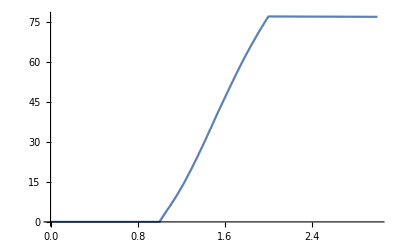

{76.8364}

```mathematica
TotalPhos= {P1[t]+2P2[t]+3P3[t]+4P4[t]+5P5[t]+6P6[t]+7P7[t]+8P8[t]+9P9[t]+10P10[t]}; 
outputVar = TotalPhos;
outputPlot=Plot[Evaluate[outputVar/.Soln],{t,0,3}, PlotRange->All]
Flatten[Evaluate[outputVar /.Soln /. t-> 3]]
```

```mathematica
paramList10fold = 
{
(*Including ek (the concentration of CaMKII) causes the other variables' prcc's to be quite small *)
(*1*) {"concCa", "Uniform", {0.1*concCa,10*concCa}, {}},
(*3*) {"ep0", "Uniform", {0.1*ep0,10*ep0}, {}},
(*4*) {"I0", "Uniform", {0.1*I0,10*I0}, {}},
(*5*) {"KM", "Uniform", {0.1*KM,10*KM}, {}},
(*6*) {"Kh1", "Uniform", {0.1*Kh1,10*Kh1}, {}},
(*7*) {"Kh2", "Uniform", {0.1*Kh2,10*Kh2}, {}},
(*8*) {"Vcan", "Uniform", {0.1*Vcan,10*Vcan}, {}},
(*9*) {"Vpka", "Uniform", {0.1*Vpka,10*Vpka}, {}},
(*10*) {"k1", "Uniform", {0.1*k1,10*k1}, {}},
(*11*) {"k2", "Uniform", {0.1*k2,10*k2}, {}},
(*12*) {"k3", "Uniform", {0.1*k3,10*k3}, {}},
(*13*) {"k4", "Uniform", {0.1*k4,10*k4}, {}}
};

paramList2fold = 
{
(*1*) {"concCa", "Uniform", {0.5*concCa,2*concCa}, {}},
(*3*) {"ep0", "Uniform", {0.5*ep0,2*ep0}, {}},
(*4*) {"I0", "Uniform", {0.5*I0,2*I0}, {}},
(*5*) {"KM", "Uniform", {0.5*KM,2*KM}, {}},
(*6*) {"Kh1", "Uniform", {0.5*Kh1,2*Kh1}, {}},
(*7*) {"Kh2", "Uniform", {0.5*Kh2,2*Kh2}, {}},
(*8*) {"Vcan", "Uniform", {0.5*Vcan,2*Vcan}, {}},
(*9*) {"Vpka", "Uniform", {0.5*Vpka,2*Vpka}, {}},
(*10*) {"k1", "Uniform", {0.5*k1,2*k1}, {}},
(*11*) {"k2", "Uniform", {0.5*k2,2*k2}, {}},
(*12*) {"k3", "Uniform", {0.5*k3,2*k3}, {}},
(*13*) {"k4", "Uniform", {0.5*k4,2*k4}, {}}
};
```

```mathematica
nRuns=1050;     (* SET THE NUMBER OF RUNS YOU WANT DONE; MORE TAKES LONGER; WAS PREVIOUSLY SET AS HIGH AS 1000 *)

paramList = paramList10fold;
numParams=Length[paramList];

For[i=1,i≤numParams,i++,

selectors={};
For[j=1,j≤nRuns,j++,
selectors=Append[selectors,(1/nRuns)*RandomReal[{0,1}]+(j-1)/nRuns];
];

Switch[paramList[[i,2]],
"Normal",
paramList[[i,4]]=Append[paramList[[i,4]],Quantile[NormalDistribution[{paramList[[i,3,1]],paramList[[i,3,2]]}],selectors]],
"Uniform",
paramList[[i,4]]=Append[paramList[[i,4]],Quantile[UniformDistribution[{paramList[[i,3,1]],paramList[[i,3,2]]}],selectors]],
"Triangular",
paramList[[i,4]]=Append[paramList[[i,4]],Quantile[TriangularDistribution[{paramList[[i,3,1]],paramList[[i,3,2]]}],selectors]]
(* Other distributions can be used -- see Mathematica Book 3.2.14 *)
];
paramList[[i,4]]=Flatten[paramList[[i,4]]];

];
For[i=1,i≤numParams,i++,

origOrder=Range[1,nRuns];
newOrder={};
For[j=1,j≤nRuns,j++,
newOrder=Append[newOrder,single=Extract[origOrder,RandomInteger[{1,Length[origOrder]}]]];
origOrder=DeleteCases[origOrder,single];
];

swapList={};
For[j=1,j≤nRuns,j++,
swapList=Append[swapList,paramList[[i,4,newOrder[[j]]]]];
];
paramList[[i,4]]=swapList; 
];
```

```mathematica
Print[paramList]
```

{{concCa,Uniform,{0.01,1.},{0.155134,0.533372,0.231074,0.428638,0.479512,0.052705,0.735233,0.950196,0.67941,0.185685,0.609218,0.0396617,0.48215,0.890797,0.87035,0.977168,0.138131,0.832159,0.961595,0.441696,0.223696,0.786356,0.0131526,0.893738,0.364829,0.289791,0.414414,0.0504574,0.415684,0.492664,0.090596,0.148189,0.93232,0.841216,0.257916,0.499492,0.409812,0.779688,0.953249,0.0958701,0.0595206,0.488757,0.235965,0.189734,0.0754525,0.0836745,0.0216385,0.363047,0.825074,0.717071,0.646289,0.769541,0.180324,0.616791,0.812925,0.470822,0.812264,0.675309,0.677376,0.825625,0.190907,0.806578,0.742285,0.804651,0.743465,0.0886906,0.994533,0.0173719,0.597017,0.294753,0.220775,0.357144,0.269793,0.848999,0.0666548,0.245123,0.728791,0.272471,0.315501,0.313206,0.887532,0.420106,0.793699,0.694668,0.051276,0.0286124,0.435439,0.92715,0.630057,0.779224,0.472236,0.390998,0.208579,0.814962,0.0970072,0.945198,0.954296,0.96944,0.429624,0.1994,0.263492,0.501656,0.78306,0.703602,0.698061,0.15159,0.55143,0.888398,0.348462,0.807378,0.691062,0.869491,0.699856,0.0560479,0.56427,0.164284,0.876304,0.124924,0.0733981,0.508731,0.542754,0.70171,0.907105,0.42049,0.968365,0.603156,0.839659,0.980974,0.218999,0.18307,0.931765,0.863524,0.329772,0.570951,0.579658,0.584134,0.862735,0.877355,0.331722,0.862204,0.886442,0.445509,0.215406,0.561678,0.725214,0.0690621,0.670925,0.0822595,0.595371,0.371983,0.974155,0.280701,0.607475,0.777731,0.559765,0.672106,0.998513,0.424596,0.407625,0.406843,0.34509,0.0262258,0.117935,0.278211,0.784338,0.814193,0.334667,0.857654,0.12799,0.183498,0.0546119,0.167756,0.20212,0.532794,0.787637,0.308473,0.171975,0.628434,0.895425,0.140284,0.270522,0.358128,0.913695,0.0792293,0.729998,0.909736,0.991901,0.632807,0.250501,0.804864,0.673331,0.157199,0.323035,0.0919795,0.496241,0.0345562,0.181244,0.549911,0.327855,0.0770604,0.281804,0.901089,0.723025,0.474208,0.847107,0.983672,0.123868,0.0663335,0.711162,0.838124,0.685014,0.339368,0.528088,0.652093,0.763127,0.669453,0.132669,0.0721078,0.919013,0.378335,0.0833039,0.993572,0.0251979,0.64323,0.191983,0.945673,0.355303,0.167132,0.85497,0.039185,0.242433,0.655273,0.605667,0.510029,0.56646,0.248051,0.426878,0.156336,0.935873,0.340848,0.040531,0.297414,0.0873142,0.979459,0.638269,0.67785,0.785885,0.800949,0.690492,0.411003,0.191467,0.941691,0.111253,0.0476398,0.963075,0.95757,0.638931,0.644489,0.129157,0.451106,0.0222958,0.978101,0.557852,0.0418884,0.915425,0.152656,0.0857751,0.0639293,0.836886,0.338912,0.928557,0.589878,0.5088,0.353061,0.125881,0.266712,0.205266,0.46073,0.774549,0.502903,0.518453,0.783964,0.911629,0.0296571,0.403327,0.642223,0.780449,0.447945,0.649533,0.898103,0.331497,0.246295,0.490212,0.452327,0.560933,0.465614,0.238382,0.0164932,0.0481459,0.225603,0.22865,0.229402,0.118657,0.199767,0.749307,0.608186,0.486467,0.801755,0.46177,0.736949,0.612667,0.700915,0.292734,0.75239,0.0148942,0.418873,0.646581,0.324173,0.288522,0.322665,0.353796,0.634653,0.321697,0.352245,0.788031,0.940084,0.568633,0.20096,0.122495,0.816329,0.68682,0.553917,0.30936,0.709297,0.892611,0.956379,0.135933,0.754469,0.823944,0.82894,0.271483,0.423541,0.215615,0.539916,0.717509,0.865593,0.186989,0.0746945,0.451539,0.459244,0.723899,0.819244,0.920193,0.377638,0.82684,0.612103,0.439736,0.885886,0.881401,0.706325,0.255355,0.951387,0.908944,0.874915,0.922122,0.997567,0.405661,0.382055,0.5411,0.867266,0.600678,0.316791,0.233523,0.673843,0.1702,0.367643,0.306743,0.120572,0.379696,0.797469,0.52022,0.0304898,0.922987,0.858803,0.305384,0.719872,0.853663,0.392521,0.146549,0.217123,0.299641,0.375247,0.130943,0.280018,0.464694,0.158521,0.166266,0.830737,0.656061,0.294121,0.767872,0.379463,0.753572,0.392903,0.758634,0.758038,0.744379,0.515621,0.494632,0.535707,0.757675,0.818863,0.50563,0.530426,0.484991,0.835285,0.173805,0.0487235,0.161646,0.975318,0.102682,0.791749,0.925841,0.318724,0.817792,0.572615,0.668946,0.726075,0.256778,0.661065,0.100983,0.0109716,0.602997,0.986544,0.0331133,0.815637,0.431195,0.0375847,0.143553,0.762247,0.659226,0.394665,0.38245,0.485587,0.453815,0.660543,0.32671,0.592234,0.262626,0.15061,0.538071,0.577489,0.776605,0.397221,0.989268,0.475889,0.17555,0.398385,0.172265,0.267708,0.598672,0.0989228,0.898816,0.336766,0.149644,0.51411,0.149309,0.416451,0.0682709,0.523484,0.9436,0.967687,0.230304,0.449568,0.86014,0.108444,0.770709,0.422841,0.70531,0.131947,0.506318,0.21158,0.790889,0.218123,0.764436,0.398951,0.222972,0.604598,0.160697,0.936799,0.8324,0.971048,0.713681,0.582452,0.424979,0.293799,0.433489,0.30178,0.720279,0.333212,0.764268,0.545575,0.666552,0.808314,0.209833,0.162529,0.412729,0.687089,0.100183,0.139169,0.176319,0.20268,0.0538099,0.307679,0.115804,0.512685,0.629362,0.731524,0.790346,0.57768,0.0694993,0.458706,0.90384,0.231915,0.0462767,0.621417,0.536515,0.689436,0.773457,0.276105,0.86812,0.97228,0.417974,0.891728,0.346771,0.718568,0.746938,0.147413,0.226196,0.153439,0.822543,0.681497,0.975649,0.206677,0.496899,0.442816,0.117017,0.613713,0.524643,0.657167,0.618603,0.372186,0.632209,0.681003,0.565862,0.587998,0.440513,0.877875,0.456733,0.511703,0.380853,0.797268,0.622032,0.0314023,0.259019,0.649086,0.623627,0.69415,0.871345,0.949045,0.55537,0.941292,0.808883,0.469938,0.772355,0.305008,0.276994,0.624581,0.654912,0.517565,0.179655,0.301322,0.219728,0.712197,0.446119,0.0850183,0.456974,0.130493,0.0356104,0.556094,0.91134,0.844112,0.751724,0.0768207,0.895189,0.212671,0.376732,0.325116,0.574589,0.820081,0.455808,0.354185,0.934561,0.0609704,0.482885,0.387709,0.412201,0.258278,0.896572,0.633451,0.937211,0.49098,0.243582,0.799311,0.141328,0.448759,0.290613,0.288102,0.873579,0.682418,0.930755,0.437784,0.517098,0.852343,0.617854,0.0367012,0.853894,0.0707215,0.061948,0.84504,0.747635,0.284449,0.105062,0.626068,0.177207,0.864311,0.959653,0.740163,0.592997,0.3683,0.454801,0.400624,0.987922,0.434776,0.842496,0.312194,0.442765,0.614426,0.924572,0.428026,0.360433,0.266098,0.111872,0.640913,0.571397,0.921525,0.750346,0.42635,0.91655,0.106827,0.188347,0.0204238,0.0944778,0.809643,0.581094,0.52259,0.637491,0.984585,0.79584,0.184897,0.768428,0.195615,0.43178,0.366712,0.65777,0.0125453,0.514859,0.341046,0.552205,0.707074,0.620876,0.958311,0.702998,0.653592,0.303752,0.90011,0.954859,0.56444,0.823386,0.21069,0.798707,0.383695,0.860807,0.504961,0.356804,0.334235,0.197745,0.667262,0.0931406,0.889105,0.665172,0.671019,0.489785,0.192958,0.337877,0.273937,0.525819,0.221816,0.531552,0.396442,0.0729506,0.75532,0.438825,0.546798,0.197364,0.946947,0.284202,0.600152,0.745344,0.704616,0.924245,0.881083,0.227739,0.884675,0.126405,0.291569,0.67593,0.350866,0.631005,0.578953,0.479924,0.342577,0.350063,0.319965,0.559463,0.745879,0.748651,0.548925,0.545026,0.0515634,0.174124,0.715165,0.775997,0.506959,0.144318,0.810706,0.36147,0.187622,0.688744,0.933513,0.915072,0.982558,0.615649,0.739727,0.692413,0.311541,0.899441,0.275115,0.252437,0.140061,0.303005,0.194152,0.9588,0.882827,0.133621,0.395154,0.240276,0.97289,0.49359,0.685835,0.727553,0.315262,0.53428,0.265148,0.241563,0.845609,0.0448742,0.849346,0.755856,0.554756,0.466956,0.480674,0.46275,0.965829,0.722697,0.576498,0.938164,0.0581405,0.548027,0.537453,0.285653,0.497816,0.110138,0.404463,0.695664,0.793341,0.635123,0.468149,0.927654,0.662802,0.734936,0.990628,0.713364,0.282781,0.961195,0.766054,0.978832,0.23806,0.771771,0.589586,0.224274,0.500951,0.236611,0.636474,0.142825,0.473528,0.850637,0.55693,0.26052,0.1708,0.386101,0.503629,0.989954,0.61015,0.53111,0.759821,0.0458124,0.761089,0.736314,0.233144,0.872633,0.856874,0.0276163,0.203307,0.906231,0.738165,0.942754,0.207399,0.346491,0.105922,0.985154,0.361755,0.103848,0.464273,0.390428,0.155843,0.165065,0.127781,0.964258,0.474928,0.060798,0.626892,0.251754,0.939573,0.102293,0.336177,0.36955,0.269035,0.310478,0.840657,0.66399,0.781326,0.730952,0.260957,0.903606,0.789198,0.446967,0.837713,0.234481,0.385213,0.0176175,0.587861,0.647543,0.606584,0.264159,0.999428,0.023767,0.86694,0.829706,0.239267,0.0106005,0.902829,0.851935,0.0879127,0.389581,0.169292,0.602051,0.159167,0.10925,0.64458,0.0893833,0.064774,0.661518,0.39952,0.640586,0.575156,0.820877,0.0250735,0.274375,0.542563,0.145023,0.726784,0.136822,0.0814757,0.373879,0.527116,0.569152,0.732403,0.359679,0.766293,0.0800782,0.929979,0.0431332,0.253996,0.460532,0.563307,0.0580646,0.432444,0.721448,0.18245,0.320281,0.693516,0.970347,0.879615,0.0341464,0.249146,0.733221,0.0925783,0.365903,0.650987,0.995883,0.878671,0.421743,0.363942,0.115037,0.544221,0.539073,0.246899,0.163571,0.679808,0.327317,0.95265,0.71579,0.57365,0.82762,0.401485,0.591024,0.651834,0.494487,0.114345,0.917817,0.295904,0.120248,0.94938,0.298387,0.521759,0.91837,0.525146,0.948033,0.625042,0.314058,0.0628547,0.802054,0.196117,0.078352,0.803652,0.68385,0.51104,0.476735,0.981872,0.611138,0.255065,0.74147,0.519685,0.581778,0.107628,0.098214,0.0954247,0.966867,0.471938,0.567519,0.213682,0.0564458,0.468374,0.299062,0.0187478,0.551177,0.873942,0.6988,0.833413,0.775392,0.794591,0.0197232,0.996628,0.528836,0.584912,0.388265,0.842769,0.908352,0.113567,0.408797,0.0322173,0.443725,0.987124,0.847397,0.483736,0.374285,0.415178,0.250289,0.586995,0.244063,0.286828,0.0422856,0.342898,0.402508,0.912795,0.409013,0.708621,0.889866,0.20451,0.178364,0.595709,0.585155,0.386365,0.477922,0.834616,0.013786,0.212893,0.34868,0.498581,0.665572,0.344208,0.317595,0.71011,0.619895,0.856599,0.992815,0.12218,0.370559,0.905399,0.96389,0.135085,0.436324,0.594457,0.883343,0.328941,0.69689,0.278773,0.598055,0.487614}},{ep0,Uniform,{0.01,1.},{0.934465,0.322437,0.908777,0.194633,0.604996,0.825121,0.879423,0.845934,0.101548,0.88334,0.429163,0.633201,0.378754,0.783585,0.707626,0.801211,0.541122,0.315807,0.0559003,0.493598,0.835489,0.0399976,0.294411,0.983241,0.124171,0.794873,0.0436054,0.263602,0.059745,0.447504,0.976057,0.0227533,0.915451,0.379739,0.709451,0.0724562,0.190712,0.642289,0.0570162,0.180373,0.4601,0.174189,0.582858,0.17163,0.351869,0.964757,0.317769,0.717927,0.739059,0.741308,0.0703584,0.5734,0.477334,0.469062,0.177337,0.441863,0.0214073,0.188704,0.726886,0.408584,0.776836,0.874772,0.576009,0.833217,0.719391,0.829004,0.609998,0.439795,0.895699,0.456181,0.977384,0.156645,0.872078,0.373425,0.913447,0.791655,0.534848,0.0199676,0.276903,0.231497,0.528641,0.630316,0.0496098,0.636895,0.782506,0.0783706,0.154284,0.0672985,0.626755,0.0923079,0.0337622,0.274509,0.831047,0.492111,0.838826,0.973881,0.248724,0.641628,0.821804,0.136291,0.544432,0.162319,0.0839595,0.272798,0.0168,0.184341,0.681294,0.54187,0.086263,0.415181,0.186379,0.357578,0.721885,0.413631,0.110338,0.540225,0.971521,0.086712,0.751282,0.518475,0.537358,0.223668,0.282682,0.583992,0.532276,0.321382,0.647496,0.201153,0.631453,0.464469,0.62065,0.871244,0.637028,0.55555,0.252395,0.218757,0.861645,0.805521,0.0739839,0.0574658,0.99667,0.112479,0.236879,0.922883,0.371602,0.0849319,0.613094,0.964158,0.273573,0.141491,0.821637,0.0977158,0.67312,0.5432,0.893903,0.864137,0.341098,0.13167,0.529694,0.315271,0.547724,0.502513,0.302353,0.999841,0.0126149,0.330409,0.474385,0.446439,0.127728,0.982243,0.0267829,0.74468,0.778246,0.595495,0.12543,0.285036,0.512558,0.706221,0.423522,0.0888922,0.29363,0.146469,0.680143,0.599381,0.0141071,0.461325,0.789988,0.924306,0.586461,0.737872,0.880668,0.849574,0.40357,0.651533,0.840843,0.0987851,0.0360907,0.481032,0.800712,0.925558,0.462533,0.430288,0.961569,0.929743,0.568452,0.899604,0.380752,0.115108,0.23917,0.185656,0.719024,0.92744,0.453431,0.700393,0.466357,0.797582,0.441579,0.374125,0.736299,0.943123,0.771864,0.664788,0.844081,0.970199,0.611047,0.120852,0.597525,0.108671,0.485048,0.275031,0.980893,0.0805693,0.255102,0.0751405,0.837482,0.235699,0.116018,0.290192,0.420618,0.65677,0.958923,0.34848,0.434859,0.466072,0.42,0.0242719,0.47979,0.834417,0.052458,0.33565,0.577775,0.769661,0.139092,0.685215,0.875698,0.806629,0.836733,0.838022,0.58109,0.21222,0.355539,0.808746,0.936652,0.16717,0.433382,0.561348,0.500281,0.896901,0.320645,0.668872,0.951817,0.0691857,0.6152,0.639723,0.0828212,0.758494,0.988896,0.872957,0.495257,0.921999,0.664327,0.338912,0.242678,0.167884,0.978709,0.0607648,0.144831,0.881859,0.927158,0.0441723,0.22201,0.892146,0.0256006,0.319279,0.652156,0.0633569,0.0932753,0.333372,0.921141,0.674587,0.916512,0.517697,0.459494,0.942231,0.131238,0.64713,0.858414,0.671446,0.615721,0.102659,0.382823,0.395855,0.604223,0.566356,0.725849,0.952042,0.603397,0.385653,0.752874,0.874243,0.753429,0.7887,0.452354,0.181061,0.948627,0.712569,0.296892,0.0425071,0.378537,0.69662,0.300488,0.105931,0.123213,0.0191852,0.901366,0.549763,0.598501,0.985752,0.488474,0.563977,0.511575,0.987531,0.577041,0.768909,0.120228,0.721394,0.196766,0.241456,0.265427,0.535303,0.818843,0.575319,0.324234,0.877797,0.193491,0.889962,0.876798,0.0956143,0.802232,0.199059,0.682445,0.516755,0.471301,0.9884,0.313212,0.326534,0.334779,0.659648,0.0877834,0.670743,0.59575,0.431122,0.218347,0.127994,0.259418,0.857563,0.676902,0.520605,0.399422,0.767614,0.807575,0.859891,0.491763,0.525462,0.445103,0.481745,0.427521,0.653538,0.957635,0.743977,0.635342,0.585335,0.107748,0.166015,0.438687,0.75539,0.130052,0.146896,0.794399,0.425606,0.607769,0.412187,0.739886,0.666567,0.140168,0.377535,0.84189,0.735174,0.94639,0.512102,0.0940078,0.991346,0.0721811,0.81469,0.928627,0.544726,0.791581,0.559561,0.594345,0.278474,0.253864,0.914216,0.587272,0.041274,0.571966,0.419061,0.12127,0.760927,0.0513978,0.683491,0.3616,0.230577,0.331902,0.0516794,0.220273,0.266573,0.343105,0.160976,0.10659,0.154146,0.144726,0.807931,0.644002,0.869563,0.910056,0.501906,0.643066,0.20399,0.847926,0.813498,0.304398,0.306836,0.449728,0.246506,0.245245,0.804724,0.650954,0.63346,0.850924,0.494284,0.730157,0.0789726,0.654175,0.840002,0.381869,0.748348,0.0459596,0.655637,0.551871,0.331191,0.386237,0.602908,0.252146,0.505993,0.256403,0.823444,0.450646,0.24293,0.831878,0.702248,0.472453,0.19158,0.0821429,0.756421,0.151229,0.325514,0.998667,0.728359,0.226316,0.766155,0.852717,0.271707,0.375918,0.289413,0.624494,0.279364,0.262632,0.967891,0.855629,0.959922,0.759605,0.731484,0.372086,0.409745,0.553189,0.786575,0.265645,0.894529,0.032783,0.286123,0.314315,0.619423,0.417699,0.358082,0.317146,0.941487,0.631147,0.925203,0.51938,0.196223,0.937374,0.250096,0.233914,0.500856,0.866109,0.891124,0.912723,0.984487,0.280702,0.334067,0.210503,0.52197,0.754638,0.691225,0.349425,0.299798,0.424116,0.780525,0.776307,0.669683,0.694073,0.665612,0.538938,0.240903,0.699656,0.939763,0.346337,0.39685,0.354591,0.690166,0.771359,0.497327,0.0534455,0.342598,0.853731,0.173367,0.765138,0.91048,0.0294089,0.401741,0.931394,0.745997,0.0158113,0.546761,0.613604,0.30409,0.437456,0.422784,0.832743,0.750551,0.525986,0.432875,0.116657,0.588304,0.394928,0.178443,0.318419,0.629041,0.287301,0.263844,0.581505,0.885106,0.618016,0.22831,0.997969,0.962785,0.888142,0.475911,0.323245,0.216287,0.237281,0.692418,0.142103,0.136644,0.498566,0.159445,0.118387,0.715186,0.451562,0.295042,0.353848,0.0809086,0.205129,0.607792,0.91863,0.990173,0.366855,0.392035,0.965322,0.103471,0.578868,0.787181,0.469621,0.365668,0.870325,0.0179326,0.907587,0.307089,0.337802,0.405025,0.192078,0.475402,0.164951,0.95449,0.56219,0.0134388,0.569726,0.856124,0.820145,0.827377,0.73829,0.824502,0.88443,0.550705,0.62139,0.129279,0.352321,0.565626,0.458648,0.675046,0.851339,0.329086,0.757148,0.930732,0.247565,0.505421,0.390627,0.868011,0.904476,0.742535,0.802976,0.43194,0.496292,0.864854,0.100525,0.134558,0.626623,0.659005,0.247676,0.720691,0.457288,0.732402,0.0975891,0.477748,0.214981,0.189827,0.311566,0.799525,0.291357,0.292098,0.406789,0.694553,0.076014,0.462921,0.0155935,0.0284121,0.601084,0.556778,0.762295,0.975319,0.618304,0.261593,0.0959467,0.612044,0.024002,0.0386756,0.722938,0.384647,0.114205,0.966108,0.867592,0.447191,0.0301445,0.425835,0.663101,0.623342,0.905184,0.56263,0.22467,0.717067,0.344075,0.365114,0.848526,0.522586,0.646167,0.785938,0.743322,0.788822,0.0322951,0.358948,0.882525,0.336578,0.72851,0.270795,0.393261,0.579599,0.698867,0.774988,0.897517,0.628092,0.693037,0.410189,0.687724,0.0206511,0.903508,0.773538,0.486132,0.933524,0.388985,0.027245,0.139319,0.188141,0.667829,0.443372,0.812607,0.255659,0.232592,0.295726,0.534103,0.119185,0.497502,0.567588,0.397991,0.179219,0.21687,0.686666,0.428366,0.415728,0.0620265,0.0403697,0.773818,0.176755,0.257729,0.280516,0.363387,0.696367,0.792786,0.950828,0.305759,0.163654,0.455606,0.829487,0.749848,0.143664,0.514089,0.672365,0.887202,0.184438,0.552428,0.817178,0.0455758,0.489308,0.209094,0.227753,0.905832,0.507694,0.400697,0.398476,0.592824,0.0748317,0.746611,0.953132,0.194994,0.4735,0.258223,0.268582,0.133906,0.487219,0.152373,0.156007,0.126783,0.203261,0.448681,0.113064,0.150187,0.286753,0.516182,0.908018,0.413235,0.147989,0.508382,0.0471887,0.828256,0.394114,0.912181,0.902425,0.779671,0.440839,0.327194,0.676145,0.523371,0.622398,0.220216,0.781847,0.43568,0.879011,0.369553,0.361733,0.206285,0.70808,0.96798,0.616573,0.570965,0.0308918,0.340522,0.625677,0.973118,0.54929,0.0109035,0.375128,0.71343,0.198331,0.862532,0.298471,0.947653,0.301378,0.208315,0.436886,0.416933,0.347239,0.560229,0.371007,0.0655454,0.935686,0.504972,0.169316,0.284122,0.557472,0.391832,0.0911313,0.584874,0.0488569,0.0112249,0.444637,0.733654,0.60961,0.893396,0.364477,0.900488,0.532947,0.5366,0.175189,0.514592,0.122793,0.853893,0.351054,0.662116,0.229286,0.592678,0.843159,0.090199,0.981278,0.384216,0.972582,0.387329,0.684266,0.797278,0.0364253,0.48693,0.945238,0.811577,0.490694,0.819773,0.099693,0.709624,0.402753,0.657477,0.158535,0.825809,0.267627,0.137549,0.961275,0.244609,0.48287,0.920376,0.747793,0.239068,0.949585,0.89871,0.0545832,0.590062,0.201774,0.554143,0.546338,0.846788,0.919472,0.886627,0.270085,0.661097,0.601634,0.528284,0.288673,0.405101,0.704435,0.151906,0.976844,0.17059,0.770356,0.504026,0.701343,0.0485529,0.955665,0.060944,0.681883,0.199535,0.679207,0.164487,0.0703005,0.524697,0.479456,0.17292,0.065885,0.991548,0.943872,0.0639788,0.0582988,0.298823,0.0347154,0.888895,0.591091,0.711575,0.0681555,0.858663,0.815898,0.969454,0.14885,0.648864,0.932499,0.809647,0.995102,0.309987,0.99586,0.312584,0.104587,0.133303,0.945905,0.816258,0.169639,0.734978,0.715841,0.703785,0.389411,0.860735,0.510297,0.0374887,0.281892,0.483336,0.957461,0.509437,0.79879,0.606008,0.710735,0.309132,0.157956,0.939169,0.986303,0.596592,0.784816,0.407425,0.339575,0.275984,0.688135,0.917185,0.640329,0.369178,0.86693,0.234702,0.571012,0.649503,0.527341,0.232509,0.530667,0.724729,0.994242,0.645271,0.557929,0.724187,0.689162,0.368267,0.211404,0.2141,0.183441,0.0776039,0.762745,0.250715,0.811035,0.328205,0.704987,0.938323,0.992911,0.956029,0.111806,0.463554,0.678308,0.359835,0.84462,0.470636,0.160349,0.76619,0.45439,0.08987,0.658229,0.109588,0.759471,0.260644,0.795907,0.979904,0.539792,0.697911,0.763528,0.213522,0.308462,0.345152,0.57433,0.222593,0.207989,0.638258,0.411028,0.421413,0.565262,0.58963,0.205605,0.778499,0.634516,0.18218,0.467473,0.730371,0.225721,0.3568,0.350308}},{I0,Uniform,{0.01,1.},{0.0736819,0.757687,0.0164125,0.469899,0.234237,0.0859585,0.406885,0.60169,0.591639,0.589203,0.0813953,0.400229,0.0353688,0.335996,0.177871,0.779693,0.190696,0.801975,0.704974,0.845564,0.561056,0.500016,0.74645,0.975641,0.888487,0.172614,0.0782706,0.997765,0.382103,0.107603,0.0233319,0.214378,0.186506,0.339035,0.336495,0.911994,0.668361,0.148179,0.198287,0.513577,0.790962,0.977705,0.439488,0.112185,0.852113,0.383808,0.741018,0.689129,0.220345,0.639595,0.0844288,0.472647,0.44782,0.221502,0.421439,0.95073,0.632552,0.733456,0.287811,0.276307,0.426724,0.149586,0.841518,0.326205,0.932038,0.466859,0.723119,0.976525,0.377769,0.414978,0.964039,0.210017,0.194035,0.57671,0.352793,0.749796,0.454481,0.839701,0.139872,0.830102,0.626959,0.356773,0.601111,0.536355,0.878393,0.284259,0.16482,0.0393261,0.559809,0.0667827,0.463897,0.456606,0.457539,0.123314,0.505508,0.442066,0.647917,0.187352,0.86564,0.15604,0.498543,0.523728,0.0915425,0.58134,0.410174,0.185574,0.43017,0.905044,0.728937,0.74332,0.448463,0.404656,0.249362,0.452538,0.889018,0.232047,0.699742,0.0665231,0.375963,0.393289,0.420768,0.75981,0.727227,0.738447,0.360233,0.834829,0.495787,0.366815,0.717845,0.212045,0.647264,0.0698364,0.0829222,0.14598,0.242564,0.96736,0.699091,0.423335,0.496574,0.894929,0.752217,0.357532,0.970152,0.828317,0.241234,0.259297,0.965068,0.835263,0.220022,0.642857,0.900955,0.906922,0.49069,0.307588,0.544631,0.39402,0.418957,0.299465,0.482149,0.0871168,0.960139,0.282748,0.0188411,0.719494,0.592114,0.579365,0.854296,0.858242,0.948002,0.468977,0.805625,0.19885,0.518253,0.450838,0.159109,0.284955,0.796938,0.544241,0.72823,0.231502,0.661206,0.104561,0.625994,0.252657,0.718462,0.734142,0.46226,0.528703,0.404069,0.0357343,0.17402,0.519719,0.671109,0.696314,0.902009,0.66351,0.38312,0.4783,0.887733,0.245795,0.41955,0.539776,0.257297,0.821399,0.130539,0.344146,0.0332513,0.0614981,0.840113,0.548308,0.80604,0.92237,0.575753,0.431036,0.240463,0.434323,0.105839,0.444381,0.364747,0.847027,0.62088,0.934013,0.395545,0.924583,0.144545,0.534007,0.127203,0.700696,0.692671,0.277195,0.636189,0.0952258,0.262273,0.0222538,0.848152,0.942804,0.205495,0.948796,0.906273,0.476389,0.408744,0.226517,0.532154,0.434066,0.873799,0.533006,0.712205,0.650199,0.248514,0.156491,0.511186,0.631545,0.795322,0.324494,0.181827,0.960749,0.280255,0.520894,0.455272,0.246868,0.895608,0.492458,0.314552,0.836586,0.367584,0.43861,0.897843,0.0565029,0.347271,0.170312,0.184735,0.800775,0.915365,0.280645,0.42708,0.784378,0.226876,0.0964171,0.999676,0.988102,0.316629,0.564192,0.838072,0.516272,0.587566,0.795998,0.820851,0.471466,0.438013,0.154521,0.599578,0.797469,0.578149,0.211071,0.131027,0.0250985,0.876425,0.272184,0.89821,0.691989,0.168623,0.275144,0.629704,0.164275,0.392617,0.938619,0.824521,0.896309,0.124653,0.771722,0.101272,0.158454,0.941333,0.873531,0.832129,0.474383,0.990474,0.530669,0.742051,0.345755,0.94422,0.929197,0.81747,0.40933,0.141459,0.0559014,0.0623334,0.0678068,0.320099,0.702615,0.133764,0.131707,0.665103,0.690561,0.773863,0.120888,0.349296,0.14759,0.400409,0.581755,0.0806302,0.232897,0.38087,0.0175699,0.641568,0.193109,0.903805,0.249861,0.521129,0.616487,0.613616,0.643729,0.562618,0.0926505,0.999018,0.328632,0.549337,0.625379,0.349924,0.0365066,0.789414,0.204109,0.76913,0.956302,0.303301,0.634282,0.237145,0.168065,0.0269342,0.475343,0.264883,0.879596,0.966394,0.0498161,0.443412,0.510083,0.0132445,0.979613,0.0297574,0.593585,0.0420343,0.369535,0.631127,0.488878,0.483335,0.0382316,0.857146,0.372748,0.239643,0.618213,0.433083,0.670799,0.0201393,0.69734,0.413961,0.281606,0.812331,0.691397,0.583304,0.244119,0.30058,0.256449,0.954618,0.0942275,0.35918,0.134938,0.669262,0.974188,0.565178,0.701464,0.0595172,0.722437,0.238481,0.0933396,0.267628,0.750636,0.916155,0.0428217,0.650584,0.848639,0.703285,0.355201,0.737335,0.243447,0.5168,0.782162,0.297381,0.566575,0.360866,0.989204,0.500938,0.762531,0.712855,0.484509,0.743805,0.866792,0.551524,0.82608,0.0387601,0.386403,0.0820731,0.996773,0.0628038,0.506728,0.770394,0.9572,0.654596,0.0247426,0.645393,0.264181,0.229396,0.440205,0.972719,0.780499,0.939448,0.0974821,0.120011,0.460154,0.373186,0.0408036,0.237548,0.982443,0.41335,0.662956,0.306557,0.446853,0.151924,0.309069,0.830718,0.317459,0.0538428,0.775435,0.157445,0.885026,0.534589,0.1157,0.117039,0.389161,0.0778052,0.0464209,0.937291,0.181264,0.984743,0.502275,0.676584,0.941764,0.288277,0.351495,0.739564,0.611944,0.133435,0.993918,0.813188,0.785715,0.0306834,0.965881,0.913515,0.870787,0.969721,0.764404,0.212847,0.121761,0.0127291,0.765466,0.849988,0.946913,0.320812,0.893934,0.43678,0.553055,0.234677,0.854984,0.422185,0.638038,0.205101,0.60413,0.681628,0.128162,0.166622,0.707629,0.483179,0.729692,0.112821,0.114672,0.674756,0.548857,0.125883,0.209217,0.503231,0.465749,0.524531,0.890572,0.329091,0.0992101,0.312082,0.877264,0.273548,0.377544,0.109417,0.610019,0.968487,0.673956,0.329798,0.314322,0.672351,0.658818,0.904552,0.292401,0.930412,0.432315,0.767441,0.87461,0.508104,0.832516,0.683712,0.108216,0.502061,0.207274,0.793821,0.0846547,0.648838,0.707976,0.716707,0.761662,0.045063,0.558348,0.567979,0.161223,0.330714,0.372009,0.78629,0.594416,0.322794,0.180496,0.725503,0.622778,0.010365,0.29528,0.951522,0.949185,0.823422,0.933356,0.962554,0.200891,0.27055,0.652646,0.52812,0.358692,0.196955,0.859021,0.311623,0.679098,0.621374,0.628066,0.540272,0.268552,0.341193,0.639833,0.428399,0.704361,0.293103,0.512246,0.733155,0.779022,0.661538,0.736171,0.160765,0.057575,0.659833,0.26149,0.883879,0.200012,0.385291,0.935082,0.680422,0.228169,0.142361,0.509366,0.0691676,0.0751555,0.55664,0.815494,0.51283,0.844622,0.0707054,0.872542,0.507477,0.169645,0.88444,0.17962,0.29792,0.446216,0.610869,0.215833,0.480519,0.985399,0.788312,0.656465,0.495316,0.353769,0.721451,0.262833,0.1663,0.677024,0.555493,0.451536,0.679668,0.909483,0.460736,0.217226,0.207056,0.607596,0.223323,0.850564,0.0270337,0.978866,0.52727,0.586968,0.524914,0.579854,0.62908,0.0309491,0.441234,0.807303,0.473758,0.824714,0.235351,0.136502,0.279573,0.0476019,0.0731521,0.987067,0.402315,0.388257,0.325359,0.342467,0.852999,0.415548,0.152917,0.397624,0.900029,0.36845,0.425716,0.864786,0.546383,0.274501,0.554407,0.391304,0.30795,0.464814,0.861087,0.334123,0.354912,0.384566,0.0445768,0.294738,0.351158,0.685472,0.714211,0.0431942,0.13857,0.822115,0.476718,0.623054,0.667475,0.0996428,0.932327,0.429138,0.175346,0.065294,0.983706,0.101588,0.129639,0.405533,0.67781,0.945901,0.809454,0.908077,0.0521391,0.754486,0.929899,0.694387,0.348153,0.417748,0.0481357,0.195323,0.327353,0.255983,0.151118,0.95564,0.777223,0.162357,0.653422,0.332441,0.71531,0.940003,0.0169146,0.113769,0.0493784,0.479558,0.271922,0.803753,0.345612,0.992047,0.596653,0.0209243,0.768339,0.807718,0.537833,0.338062,0.118365,0.177566,0.0115815,0.171858,0.861917,0.826818,0.542899,0.450218,0.0903101,0.862579,0.504366,0.809593,0.65821,0.0341841,0.110074,0.68501,0.491421,0.799951,0.609586,0.720831,0.458793,0.655199,0.791916,0.43559,0.68251,0.802353,0.535245,0.753582,0.842615,0.467488,0.566258,0.285473,0.208145,0.877869,0.972152,0.81083,0.914473,0.538514,0.711429,0.103764,0.792983,0.986731,0.635305,0.253798,0.32395,0.218867,0.891853,0.562251,0.0227406,0.0604707,0.462794,0.553989,0.869164,0.140913,0.595194,0.259864,0.776007,0.957693,0.21806,0.254421,0.615956,0.267356,0.856294,0.290042,0.597943,0.748229,0.118588,0.45894,0.574247,0.952013,0.52954,0.595862,0.162883,0.374205,0.815189,0.310187,0.0288137,0.697651,0.990978,0.411776,0.598755,0.92275,0.145211,0.568876,0.651629,0.918513,0.859784,0.981479,0.70904,0.0978435,0.136053,0.0142765,0.64203,0.730522,0.088011,0.269963,0.251394,0.318451,0.920476,0.192427,0.961815,0.863781,0.746001,0.189944,0.424022,0.202593,0.478752,0.633949,0.176174,0.370763,0.706065,0.401301,0.995118,0.585578,0.0892591,0.0645446,0.379674,0.818938,0.575103,0.196623,0.844335,0.85132,0.740489,0.92804,0.142957,0.925652,0.387171,0.493595,0.291684,0.923736,0.944446,0.570862,0.277923,0.744604,0.188523,0.921214,0.305733,0.250501,0.782658,0.992818,0.397373,0.787204,0.201777,0.332548,0.710181,0.540947,0.911113,0.751756,0.714804,0.763416,0.17485,0.444767,0.970801,0.398503,0.34334,0.0715244,0.617619,0.36265,0.224737,0.624033,0.606232,0.766184,0.890808,0.773056,0.304592,0.222665,0.245466,0.918974,0.230246,0.546632,0.867488,0.725789,0.778343,0.489179,0.315661,0.569242,0.321921,0.819575,0.411429,0.75519,0.731588,0.111362,0.102558,0.665559,0.995964,0.302565,0.79049,0.126229,0.340228,0.572822,0.590341,0.494548,0.375369,0.182977,0.0512063,0.816762,0.286334,0.487018,0.0761893,0.266382,0.298576,0.828878,0.517952,0.0323508,0.981056,0.522321,0.602871,0.312998,0.302095,0.0550271,0.137519,0.882329,0.258681,0.571441,0.724414,0.893021,0.584598,0.0152354,0.605167,0.760835,0.542113,0.833758,0.582856,0.882055,0.975406,0.416557,0.559286,0.514617,0.470472,0.453216,0.687222,0.0745549,0.379134,0.0886334,0.686773,0.608354,0.396457,0.783786,0.901152,0.952931,0.735886,0.657731,0.868661,0.0528778,0.772706,0.646298,0.0792733,0.886482,0.497745,0.936246,0.673723,0.573216,0.289696,0.694686,0.339416,0.871721,0.756097,0.39075,0.215363,0.637012,0.154124,0.687968,0.365485,0.603821,0.334609,0.917606,0.748818,0.191714,0.48552,0.613287,0.666776,0.757372,0.588887,0.122446,0.525765,0.959321,0.557219,0.550842,0.909795,0.91269,0.619506,0.615237,0.926723,0.758712,0.798899,0.487577,0.837688,0.184374,0.841776,0.0584444,0.295966,0.880426,0.22553,0.106492,0.361745,0.804578,0.364011,0.149362,0.407811,0.813469}},{KM,Uniform,{0.04,4.},{1.49282,3.70935,0.934031,1.77993,0.386618,3.44259,1.63494,2.38528,3.94732,2.95252,0.129747,0.201315,0.48896,1.97543,2.22876,0.757624,1.9683,0.751562,0.097066,3.37671,0.552736,2.6549,2.4074,3.36375,3.32131,0.179882,1.98301,3.29733,2.79288,3.03321,3.94312,0.546846,2.80241,3.83263,3.70962,2.93856,3.31233,2.1582,2.90125,3.93566,3.96181,3.40291,1.64851,1.6839,1.34975,3.64318,0.246449,3.62826,2.10243,1.69604,3.75539,3.10889,1.56581,1.08944,3.88971,0.518298,2.26398,1.47355,0.123598,1.12556,1.26485,2.77439,2.09234,1.90514,1.78835,2.40107,2.73744,1.14787,1.14442,2.57415,1.01855,3.39473,0.233255,1.52412,2.9208,3.80111,2.39834,3.73972,1.38941,2.14704,1.50578,3.52859,1.56872,2.21759,3.62035,0.603901,3.72471,1.24886,0.906046,1.18429,2.16382,1.30024,3.06745,3.7827,3.13169,3.85264,2.79568,0.799975,3.70248,3.50438,0.30618,2.81472,0.716911,3.97728,2.92189,0.379175,3.06032,0.197044,2.91108,2.47705,1.43772,3.00969,2.46315,0.562219,0.0433308,0.659968,0.215577,3.21651,1.61707,2.07617,3.17411,1.52802,0.118791,1.14972,1.0753,3.44716,0.958362,3.65252,0.423532,1.67431,0.65325,1.29892,2.5353,2.05437,3.74459,2.76608,3.25278,1.92484,3.25401,2.23762,1.7479,0.073552,3.91031,0.47099,2.41396,3.92782,2.00129,1.45819,2.49216,0.527906,3.9237,1.71042,0.632882,2.96649,3.40778,1.08578,3.71928,3.38408,3.20331,2.53882,2.88098,1.93448,3.07594,3.00164,3.79388,2.05962,1.4329,3.46407,0.720805,0.144008,0.166795,1.44453,2.08266,1.60317,3.50744,1.9922,2.41937,2.89557,3.26036,1.85025,2.21173,1.87123,0.600985,1.05496,3.93738,0.451496,1.8892,2.66823,2.54319,3.99152,2.51669,0.950166,1.04433,2.51164,1.27636,3.87742,1.87751,2.75359,3.72879,2.44258,3.15435,3.78038,1.22372,0.383064,3.61272,0.790945,2.26516,3.41256,0.082804,1.12859,1.19109,1.33774,0.97445,2.79848,3.14536,1.85254,3.02714,3.19556,1.20733,2.28102,2.29401,2.71352,1.95595,0.141415,1.40262,2.98835,3.63491,0.0542709,1.28789,0.35551,2.01626,0.371874,3.60272,1.38471,1.22678,3.79986,3.34437,1.49593,0.848787,1.45678,1.11628,2.4334,1.42157,1.12062,2.58302,2.87016,2.269,2.13044,1.09697,2.37448,1.1759,0.0487099,0.477669,2.8594,1.49063,0.876409,0.505037,0.349493,2.74343,2.98384,1.47771,2.25705,2.07157,1.42583,0.157086,3.1874,0.499609,3.30262,0.536447,3.4941,1.10096,3.65484,0.897635,1.05231,0.724984,2.61898,2.32582,2.18841,3.99408,1.94681,0.815638,3.00686,0.672798,2.54472,3.95762,3.58109,0.523003,2.11704,1.17501,2.55509,0.641308,2.87555,1.2666,0.108893,3.1103,0.220918,3.34892,3.43924,1.25989,3.09312,1.4107,1.20057,3.2145,2.38891,0.84396,3.07766,3.76119,2.60724,1.85917,3.17014,1.59808,0.948712,2.55094,2.96716,2.84075,0.664892,3.0005,0.606069,3.46493,1.76135,3.84774,0.628908,3.42696,0.586174,3.66871,0.0773079,2.25008,1.65714,3.91405,2.90507,2.13911,1.414,0.695299,2.53284,0.162779,3.61596,0.106779,2.52478,0.0637867,3.65702,3.60871,2.43994,0.911991,3.26277,0.650573,2.10319,2.50198,2.49036,0.938463,2.62468,3.0637,0.955158,2.90738,2.18108,2.59865,2.42568,3.47824,3.37112,2.04188,3.32508,0.870145,1.39761,0.430656,2.41187,0.361533,2.2035,1.33153,0.310544,2.60259,1.68755,3.87519,2.64465,0.456317,3.36081,0.262978,1.4181,2.74684,0.823456,1.71443,0.267457,1.78435,2.39339,2.75768,0.922637,3.48067,2.70514,3.93153,0.442004,3.63352,3.51802,1.38075,1.66874,1.71989,1.69148,1.86412,3.77152,3.97254,0.131698,1.81407,2.69964,0.208103,0.111932,3.1352,0.620579,0.82697,0.170324,2.13555,2.81898,3.54524,1.42822,1.63768,2.35829,3.64788,1.08035,2.31211,1.16773,0.835165,1.10737,1.79219,0.436715,1.32092,1.57697,3.052,3.35312,2.30229,1.03779,1.32356,0.67697,0.420318,3.30903,0.761776,0.778155,3.67546,1.62554,2.56462,2.93327,2.20565,2.37554,3.5699,2.46875,3.70075,0.802669,1.48681,2.44824,3.28683,2.76858,0.37347,3.56443,2.5273,0.965186,3.76251,3.22493,3.19232,0.610363,0.828467,0.573919,1.46771,0.10191,0.588001,2.69053,3.10578,1.98708,0.628075,2.50567,1.57212,1.7775,2.32068,1.84383,1.30435,2.4587,2.77125,2.03451,1.36426,3.49745,1.8343,0.367305,2.64833,3.01816,0.679924,3.10217,0.293265,2.4734,1.64335,0.222156,0.578236,0.339308,0.770111,0.292636,1.0723,3.52159,2.91389,1.6148,3.66651,3.12352,0.532131,2.18301,0.334439,3.67789,2.01522,1.88604,0.852843,3.1172,2.05009,1.1895,0.444652,2.09675,2.95096,1.39982,0.0666068,3.62486,3.16299,1.8571,2.21526,1.73417,0.358984,2.82821,3.27809,3.52518,0.258578,1.96292,3.12665,1.35478,2.62996,1.3606,0.299444,3.82214,3.04245,1.90925,0.991853,2.43583,1.91814,2.80802,0.482249,3.01295,2.37008,0.764545,1.57985,0.343687,3.05555,1.13505,1.24615,1.99481,1.8987,2.92767,0.230852,3.22919,1.2348,2.74974,1.97161,2.7307,1.95231,0.820409,1.03282,3.72309,2.99499,3.88193,0.858853,2.4856,2.76023,2.47136,3.68867,1.19417,1.20957,0.553105,2.22414,1.67812,2.65972,0.40989,2.19028,2.72241,3.20873,2.37936,1.56313,1.59306,1.62052,3.4988,2.36241,2.33496,3.41988,1.79993,0.176671,0.579705,2.24964,3.15948,0.119709,3.69496,3.55108,2.3045,3.33464,1.23967,3.9471,2.57648,1.82451,1.80346,3.04618,3.27587,2.32223,1.94852,2.78462,1.13096,0.392495,3.89564,1.34452,3.96369,2.99178,0.894259,3.36728,2.58033,3.68304,3.43593,0.466048,3.717,3.19852,1.02542,1.34633,2.65033,1.96391,2.82676,2.36582,1.46288,3.23257,0.188176,2.34254,0.902088,3.24882,1.81834,3.64094,2.94774,3.53658,2.61061,1.76589,2.85322,1.48081,0.348524,3.82889,2.14082,1.18126,1.00781,1.06573,2.5197,0.701655,2.58639,3.22251,3.98784,2.11121,0.807954,3.41072,0.908231,3.23609,1.65874,3.08313,1.15411,3.12121,0.152027,1.83626,3.89952,1.23558,3.45387,3.15053,3.26554,1.93745,3.5604,3.04046,1.16426,0.275142,2.17434,1.51451,0.984416,2.55885,3.81689,2.67897,0.153208,1.53798,2.06713,0.794968,1.35955,2.62062,3.53523,1.37855,1.25479,2.97756,1.80595,2.24438,0.837075,1.61006,3.96901,0.885577,2.31492,2.69172,1.59551,0.046013,2.27684,2.2747,3.03466,3.18107,1.64116,3.14281,2.33752,0.715035,0.300356,3.98233,3.88432,2.35315,3.51282,3.80716,3.38657,3.23845,1.54504,3.51577,2.67592,0.318385,2.73378,0.734463,3.59783,1.25304,2.86637,1.90155,3.89128,3.45143,1.82244,1.99753,0.33094,3.46016,1.27899,2.9628,3.07205,0.773542,1.83953,1.91992,3.60767,2.16225,2.78024,1.74007,1.20478,0.990255,1.23068,1.40569,1.65161,2.01245,0.890344,0.253696,0.261863,0.540675,1.50073,2.06377,0.613479,3.37956,2.29603,3.84169,1.9795,0.80995,0.466769,0.226569,2.72078,1.36858,0.597419,2.28766,0.638925,3.58653,0.402069,3.58328,1.00015,3.76638,1.77171,2.9787,0.742288,2.03645,0.864802,1.73116,1.51724,2.34844,0.184279,3.18224,1.06711,1.52031,2.05111,1.44003,0.8799,1.39256,0.427168,1.74213,0.570855,1.28394,2.82272,0.0871171,1.663,1.70639,0.623044,3.57493,3.91838,2.12375,0.559968,1.70057,0.461315,0.284454,2.69712,0.511775,2.63388,2.22279,2.72864,2.24248,1.04051,0.203341,1.55255,0.929773,1.94391,3.29269,3.74279,2.19684,3.78946,2.8616,1.79582,0.249503,2.92911,3.68612,2.68466,0.656295,2.15248,2.3088,1.63115,2.2315,0.857478,0.739937,2.42099,0.326921,0.696691,3.3414,2.71406,0.941399,0.271848,3.9989,2.84451,3.59349,1.53635,0.785984,3.08575,3.5409,3.8387,2.95691,2.61461,3.32963,1.13765,0.389949,1.2951,1.33538,0.172239,2.00538,1.09392,2.56192,3.74855,2.33099,0.325011,2.87672,2.29112,2.19818,2.68079,3.90712,1.44808,1.06114,1.67136,3.33691,1.60705,3.28281,3.81111,1.2698,1.91111,0.400223,3.83423,3.17093,1.69485,2.17554,3.87086,1.08452,0.407229,2.89492,3.31864,3.31516,2.8564,0.194272,0.0558965,0.747031,2.3914,3.48684,3.66208,1.89264,3.90524,1.50861,1.04758,2.71014,0.869316,3.75179,2.66284,3.42592,1.21971,2.51022,3.48795,1.88284,0.841491,0.710872,0.541789,0.521806,3.97743,0.995576,2.66951,3.46944,3.09029,1.10493,2.17002,0.13792,0.917271,1.54966,3.55225,3.85625,0.691419,1.11306,2.03009,2.81057,0.280356,3.78524,0.931217,0.0811235,3.69402,1.3094,3.30092,1.1571,2.45532,0.476068,1.29003,0.882623,1.55656,2.15153,0.567564,1.31388,1.53208,1.77074,0.0916149,0.5033,0.978474,3.20631,0.236659,2.12771,3.85823,3.77599,2.48172,2.94052,1.01529,3.24205,3.73398,3.15653,1.54376,3.27105,2.63955,1.71654,3.28866,2.10721,3.86215,1.02888,2.83638,2.02509,0.647066,0.28731,1.82985,0.396317,0.753039,1.21497,3.4002,3.81376,2.0457,2.49611,2.11904,3.01991,3.8261,1.87524,0.315072,3.86634,2.83291,1.75745,2.07697,3.0958,0.448753,1.5894,2.45166,1.45409,3.5575,1.47144,3.41841,2.09155,0.0613653,2.89038,1.58292,0.780648,0.667287,1.72922,2.25993,0.980538,2.08751,2.88496,3.35712,2.59103,0.729403,1.74876,0.149325,0.211921,0.433444,0.415111,2.5679,0.968182,3.47406,2.63631,3.3924,3.02663,3.5708,1.81255,0.321665,2.84909,0.733313,0.592659,1.75549,2.34617,0.789863,3.95376,1.92632,1.02139,3.43115,0.682415,3.59217,0.0950898,1.16099,2.78611,0.511132,1.31673,1.72247,0.706988,2.43096,0.920952,1.92958,0.961388,3.13754,1.32874,0.493968,2.02269,1.37239,1.01012,1.00346,0.485815,0.688184,2.59401,0.243401,2.97411,1.86913}},{Kh1,Uniform,{0.4,40},{36.2786,24.6581,28.5213,32.8213,18.5575,5.03413,30.0661,0.998164,13.687,7.7815,6.37074,13.9416,39.0446,21.2441,1.79965,38.0651,37.9383,27.4486,27.9319,27.7294,23.2789,37.6605,7.16621,25.3668,39.2955,3.02017,30.44,12.2023,5.36822,18.1883,36.5867,8.24821,17.813,2.13867,14.1574,2.45834,1.6329,6.0878,39.416,6.57476,19.84,7.81538,2.20607,25.8134,6.65178,13.4422,10.2822,36.2393,35.2201,4.46899,15.136,15.1062,15.0406,13.657,1.52061,15.2813,9.20813,37.2099,9.83929,34.0245,26.6307,7.10109,12.5107,12.3419,22.5749,37.4619,35.579,7.54335,29.2706,17.0233,29.951,1.13736,6.67346,19.6529,24.2062,3.05046,38.5109,25.5192,37.9175,18.7756,33.262,22.9098,35.2842,33.5593,17.6168,6.87086,18.0158,35.6914,36.7498,3.86647,3.65145,6.349,4.87291,22.24,39.8546,26.0321,13.727,16.4552,8.74774,39.5863,30.3033,16.5323,20.0801,2.76733,26.7017,5.09966,39.2538,38.691,20.8089,38.9325,12.5551,24.0916,21.9219,30.9884,27.6067,9.28976,25.595,18.2172,33.9508,17.6664,31.1282,20.3694,19.4167,19.6138,19.2627,27.5681,30.4105,4.15674,20.4233,34.0489,19.4772,10.1759,25.4124,12.7949,35.4298,29.104,2.64442,15.1708,3.42763,18.7431,31.2832,23.5462,10.2304,37.042,18.0005,33.4261,3.93361,10.4919,11.2138,8.11636,37.2582,17.3867,26.9892,22.9479,38.0067,18.3919,11.2707,3.7458,29.5323,5.39968,37.0884,27.6801,11.3537,34.4089,15.7745,28.7857,14.5385,31.975,6.25137,3.87335,16.6871,33.6928,25.7257,12.4488,14.6235,20.6453,8.91725,6.70817,37.8334,24.1432,31.6335,23.6435,3.36266,38.6671,16.1373,5.65326,37.379,5.53224,32.4821,9.45171,35.9821,17.1321,5.14788,14.9188,22.4394,16.864,37.5845,23.7619,3.16003,1.27626,24.2771,20.7399,3.54334,8.98145,21.0486,10.4532,20.8945,0.575171,9.77298,12.4163,3.39416,22.4639,27.3262,27.8322,39.1164,25.1462,1.48466,1.1121,23.9599,16.2772,10.5386,3.19636,5.84178,5.73249,23.0047,16.3836,28.2995,16.6094,18.8699,36.1698,15.5387,17.3269,5.042,14.3855,0.501409,18.0714,15.8513,18.2461,21.5713,7.35228,27.9707,26.081,36.6162,39.763,28.8842,13.5669,19.7924,0.860405,28.9154,33.1871,25.2645,26.1642,13.8801,34.4265,36.0879,17.8987,4.9159,9.91523,1.91526,2.25374,36.8118,13.2804,28.2364,21.3921,37.1441,4.73542,2.55066,16.1882,9.94968,9.14744,4.07043,10.8741,12.2715,14.8437,31.0949,39.7863,34.5223,38.7519,18.6658,9.17885,17.7348,30.2526,17.0677,34.2086,8.65596,25.6835,28.1085,21.4274,20.4854,28.8092,33.7808,7.85876,7.93076,38.7976,15.4201,7.64433,31.9297,15.0064,21.8199,23.8841,22.056,1.75604,39.1533,39.9806,12.3109,4.39497,11.9727,5.18168,22.1565,33.3131,13.8239,24.6997,7.51079,20.1473,35.2041,17.4146,30.0957,9.87637,1.04006,13.2105,17.4607,27.4044,33.3707,37.975,1.77424,34.9548,4.94266,5.5048,25.6363,1.17325,30.7336,22.727,9.02322,5.21982,16.7153,14.6943,31.1524,14.1663,31.0502,16.5582,22.7266,11.5628,11.5186,2.04325,13.3527,8.81732,18.7187,2.94298,34.5565,35.9549,10.1052,35.8106,24.9396,14.3239,28.3311,31.336,13.7706,38.9451,20.4578,37.3468,15.3731,37.0024,17.1712,9.43497,14.5763,7.8867,30.136,33.7435,23.5036,1.05812,11.146,21.1313,35.6565,23.0717,18.9275,33.1301,12.7196,36.9673,25.5588,8.45301,26.9411,7.31431,23.4545,30.5298,36.4542,12.7587,21.8569,30.8894,27.8077,30.1799,2.12575,8.58689,25.2415,11.7893,10.1367,0.844298,3.23227,15.5695,17.9248,32.345,9.37019,13.9983,29.6705,34.9955,26.5598,28.7416,29.556,30.5457,5.76893,27.1833,25.513,19.0467,0.813678,7.20817,4.04787,20.9368,23.7278,11.024,10.911,2.53289,6.11422,9.08492,28.6826,36.6939,12.6744,15.8108,3.58616,6.53952,18.9951,38.1373,7.41611,15.7271,24.7261,19.5033,27.1263,2.50983,22.5204,17.7526,35.4719,0.618852,31.4617,5.22813,2.89204,35.8751,34.8004,31.7045,34.3128,15.9041,1.24756,25.9786,0.771287,26.7688,20.5295,14.3113,6.1869,6.95847,20.6879,31.4171,7.96469,4.83687,20.2667,5.69586,34.1043,16.5031,20.1737,8.80576,6.16117,24.5293,13.4828,15.8678,3.69992,29.5977,33.1578,19.327,0.938262,12.0239,30.6888,10.2541,14.0447,18.602,5.98774,33.2169,32.6681,4.24742,34.7054,31.5693,24.7679,19.8831,8.8823,18.1263,29.364,31.1933,3.95879,32.1468,22.6154,5.33479,28.078,36.8374,1.89078,35.1383,17.5878,3.08475,35.8277,39.6461,27.2578,38.2998,23.3056,21.7027,3.80683,32.963,35.4776,32.761,21.7642,4.49987,31.4841,10.6293,2.84882,31.3125,39.3511,3.33028,34.1906,37.3986,24.8641,33.8267,22.3423,34.8757,38.7813,33.0163,25.1376,31.8066,29.6366,1.98127,27.6494,30.3148,16.0927,28.9524,32.5968,24.267,16.0031,24.9039,0.441595,10.6661,11.3255,7.47286,11.8447,23.398,4.64862,21.3546,23.7885,35.1157,9.98104,8.67192,38.5738,7.1159,34.758,1.71912,20.0442,13.9359,32.2811,4.69365,20.8734,20.9566,12.0834,0.703263,11.4747,0.523066,2.6724,36.2166,37.1752,28.0113,36.0086,37.6038,35.7677,2.61774,5.47476,31.2453,24.4154,5.60549,10.3742,39.1982,14.771,18.9886,12.2422,28.8672,24.6305,10.089,19.777,5.57331,11.4068,8.5828,7.26748,22.989,14.6899,22.6676,20.578,38.1527,11.7457,11.8735,1.30573,36.0639,14.0901,13.3162,29.8943,16.8323,25.9425,33.0246,16.4022,14.9767,26.314,21.4876,13.6311,15.6448,10.5614,24.5393,32.3084,33.89,38.623,33.4383,11.2441,30.9346,7.62067,25.8769,26.6741,12.61,15.9393,36.8986,26.1541,6.21163,14.586,5.95333,25.3186,32.6164,37.7332,9.68611,19.9872,5.89874,22.7909,28.4785,22.3548,9.62767,12.4988,22.0236,29.7624,13.0331,31.3795,4.10678,8.13657,2.97865,19.0843,31.605,0.892567,19.9488,13.511,11.083,35.34,30.5932,26.4133,6.31485,21.0216,16.9572,30.6498,13.2388,29.7925,1.59562,28.6219,2.79743,9.65127,10.9463,8.01874,24.1715,33.5045,26.4433,9.79986,22.3924,34.1541,4.23116,10.6071,23.9185,28.5421,27.1008,14.8658,38.3149,2.23121,4.34329,4.61433,3.79026,3.5077,14.2503,32.1135,33.8952,4.41832,1.22154,26.8182,32.7081,5.92682,24.9812,32.2562,1.41963,16.2106,19.2338,7.98783,1.41211,34.5844,27.3517,35.7288,20.7056,2.73459,27.0541,39.8934,22.0961,28.6033,9.73655,14.7449,33.9733,17.2093,19.5438,16.2814,21.2819,32.8402,38.5649,14.4718,4.75704,24.5869,4.19773,39.2309,2.09393,19.9293,39.8301,3.29812,12.933,20.7691,38.0916,4.01442,25.918,13.3739,37.69,20.2242,11.0668,14.4351,19.5901,9.0477,23.5603,39.5528,34.2536,1.56895,15.3098,39.4433,8.40438,35.9101,6.607,32.3853,6.97875,26.2736,16.6341,33.0619,31.7648,37.7665,39.3933,10.4283,26.5143,12.3851,5.00025,2.43277,5.8184,0.670757,29.8226,32.9392,17.9511,19.7384,19.3556,38.2106,5.43441,11.6295,23.4191,34.9459,7.56984,23.856,30.8636,18.3371,6.84491,31.8674,16.7863,10.7617,3.12779,29.2182,34.609,21.8802,6.49701,27.893,26.5973,13.5465,10.3379,9.51341,9.58239,3.63504,26.8827,24.4302,38.4499,23.6952,16.0236,8.36436,11.7033,21.526,35.0816,30.3511,6.79737,2.85212,18.5358,7.00331,29.3127,29.4477,17.5402,8.51598,25.7781,17.8553,32.8869,25.8478,5.28008,25.0397,28.9929,24.0692,24.8169,36.359,27.5028,18.0918,23.3618,11.4133,33.3475,38.8782,34.7511,12.9093,32.05,29.0797,16.9532,30.4733,21.1852,8.70894,38.3698,20.3284,25.0162,17.6824,18.9014,32.7537,15.5167,8.96103,7.4087,16.9041,29.1453,27.3732,7.07448,27.554,9.23327,13.0387,34.4598,28.722,15.3656,22.1991,35.5215,32.4355,22.8667,14.9298,15.6925,29.2043,9.54657,36.5533,30.8255,36.3808,39.085,6.41091,18.3884,23.1302,29.7238,19.6831,33.6628,36.4626,9.30401,26.204,29.4846,28.379,36.1348,23.0552,26.3522,11.1787,33.7168,8.50404,12.9843,17.0753,6.44239,10.7844,21.6109,26.9787,0.656188,39.0078,23.2512,22.5929,36.9371,8.33711,29.8886,39.7246,27.9006,12.0945,8.17287,23.2021,30.0223,12.0121,36.5189,7.72368,35.2884,37.2919,19.3788,4.55339,15.4707,35.6238,18.8116,33.5914,38.478,19.2109,31.5202,22.2955,36.6595,7.24812,32.1667,37.5429,28.1858,22.8341,30.6321,26.468,39.6626,21.9985,12.8596,19.1714,21.4644,10.8331,20.5675,2.32873,17.3361,4.51659,29.9796,37.7765,10.7165,38.3935,27.7503,17.2695,30.2031,12.1651,26.8419,2.39223,24.3578,1.9898,21.9528,8.23409,8.08711,24.3268,11.5762,6.0245,34.3614,16.0557,28.2276,31.9001,15.6365,13.8352,13.0925,38.2602,28.386,18.4908,24.0034,26.7605,14.211,30.9708,21.6357,6.89792,3.48853,13.1839,25.0746,39.4787,29.0548,26.2434,20.0893,32.0226,10.0275,35.0553,1.65241,0.401892,31.6776,28.1565,11.9231,18.6227,15.2526,18.4525,9.38729,16.7413,25.48,8.30648,2.29621,4.29747,36.7864,13.1413,17.5142,12.6196,14.0998,27.2325,11.8111,25.1789,28.4572,34.862,21.7299,23.6283,16.3251,38.8461,21.3304,11.64,39.9445,23.1502,29.41,24.4627,18.2869,26.1206,34.27,34.6627,37.1104,35.3722,25.3967,32.5663,32.5058,30.7974,19.1407,27.1576,15.2047,4.80076,20.2979,7.68072,29.3962,37.8846,39.5215,1.84784,24.0411,12.8285,31.8495,6.74779,32.2015,1.3579,17.2275,10.9965,36.326,14.4029,22.1823,37.5107,21.0955,33.5252,21.1721}},{Kh2,Uniform,{0.07,7.},{2.83511,3.26249,4.73853,3.39952,1.46728,2.9186,2.89379,6.18476,4.44166,4.68282,4.89118,1.86507,3.32159,3.62303,5.05708,6.52621,3.52825,5.73285,6.64829,2.41455,4.73347,0.449322,2.84511,6.14206,1.65603,1.49276,5.32674,2.01906,3.1469,6.98549,4.37935,6.51588,4.49975,3.93829,3.80072,2.77641,6.17223,6.18148,1.83751,4.35066,1.83895,2.57888,2.26373,1.49631,1.82788,4.60172,3.05875,4.68429,2.21974,6.35813,4.18575,5.07576,0.548616,5.55803,0.221436,5.26971,1.02005,1.28399,1.37453,5.63954,6.28345,0.877414,1.2324,3.91789,3.72123,2.86473,3.58423,0.841194,4.69316,4.1482,3.36268,2.33437,3.25586,0.514548,4.09996,3.85013,0.416723,2.11206,2.19831,0.687971,6.5689,4.45395,3.60258,6.10312,3.57334,0.0865569,0.725224,6.15649,4.88788,5.44245,5.71146,6.24676,6.43796,5.25496,2.88109,0.713248,4.45064,3.77913,3.23555,1.52505,6.39759,1.3956,3.80595,4.78151,2.62697,5.5745,0.333935,0.822899,1.79641,2.38667,5.88843,5.30864,1.04667,1.77468,1.3594,2.54095,4.57711,0.747068,6.1638,4.16554,5.23797,0.263532,3.54208,2.56051,4.36716,0.311619,2.99566,0.504986,1.93388,4.31601,3.97541,4.46019,6.80042,3.4266,2.61156,5.28112,1.5324,6.47042,4.01591,4.21411,4.40177,5.80098,2.87438,3.28293,6.42224,3.42221,0.805117,2.45257,5.93927,6.58377,1.1535,1.51394,2.98998,0.113059,5.46167,4.54229,5.53535,1.12778,4.83142,1.63356,6.88847,2.32522,6.40009,0.749812,1.21563,3.36708,2.41017,4.84285,2.72345,6.67591,2.77195,1.74002,5.9911,3.31153,2.70318,1.51643,5.59152,4.03379,4.34087,2.02673,6.55573,4.84065,6.59171,6.71996,1.47428,5.21953,4.22062,4.87949,4.43461,5.72895,2.93748,0.235826,3.6548,5.42549,0.422454,6.62083,6.81366,4.41144,5.9685,3.44728,0.614541,3.79148,1.40102,5.83132,5.78317,4.94288,2.60404,3.17406,2.40432,5.89308,1.41114,3.34168,1.58594,1.55761,3.34361,6.58712,6.34838,5.48544,2.91078,4.56897,5.34158,5.40101,4.90185,2.09375,3.51212,2.26811,4.28566,5.47017,5.86183,4.26696,5.0888,1.80424,4.13219,6.32878,3.69725,5.71812,2.18883,2.98542,2.74738,2.65978,0.2519,5.10174,3.24131,3.22486,4.86115,1.40337,5.08282,6.25188,5.49694,2.22188,6.60608,4.05672,3.85203,6.20944,4.30111,6.80505,1.22105,3.77127,4.7277,2.74225,4.37996,5.65121,2.46058,3.38346,2.96177,0.648916,4.95086,2.6441,2.49773,4.92779,1.88663,2.79095,2.52282,4.22942,2.54786,5.93273,1.20986,0.964823,6.08566,5.41411,5.09379,4.65685,5.48156,6.83847,0.492038,5.18691,4.41449,0.0800976,5.07057,0.572561,1.30283,4.27722,5.57217,6.431,2.20667,3.9153,2.76735,0.212708,2.31344,4.71502,5.50425,5.40503,2.29869,2.51381,6.13361,5.51902,3.95373,4.32871,3.61582,4.66792,1.1791,4.29592,3.57808,6.2001,0.856216,3.06112,1.56305,2.63905,6.11016,6.45652,0.161759,3.33491,4.49198,1.56824,6.51021,6.47664,6.09325,3.7332,4.00452,4.97702,2.0965,2.67678,2.27768,5.13116,1.13278,4.74779,5.77733,1.50682,4.98262,5.60876,1.70361,0.184467,3.94521,3.6675,6.10179,1.73765,4.36625,1.75791,4.42769,3.87694,3.41255,0.97343,0.580085,2.69116,0.592169,0.721067,3.97897,3.10259,4.76845,6.78984,1.00299,1.97646,0.395258,1.74923,3.35148,1.27396,2.13564,4.54855,3.83857,2.35538,6.31537,0.816617,2.03513,0.476073,4.20539,2.57561,3.64914,1.35067,6.68407,0.997715,0.66851,4.82154,4.78865,2.17765,0.993588,6.86305,6.48557,5.79467,6.75453,3.70696,1.99035,6.89906,5.20716,3.89942,0.552253,4.25812,0.95919,2.95309,0.510229,3.95888,2.78738,4.75588,2.15637,5.63213,0.629835,3.63948,0.907931,6.30958,5.69121,1.10701,4.82405,4.77009,2.05763,3.01103,4.49299,5.93012,4.79065,1.7841,0.339991,4.8153,0.951545,3.02297,1.11653,4.52769,6.01725,1.95862,3.66067,1.2387,2.61078,1.87585,5.52482,3.48986,1.63437,2.92574,3.685,1.65073,5.44219,2.25135,1.55432,3.93663,2.47341,1.3499,5.88221,4.99048,4.46763,6.33387,3.55919,5.65722,1.4623,1.33324,3.21955,4.96648,6.65457,1.05473,3.1143,5.15352,4.04999,3.9911,3.12365,3.0866,1.08701,2.25816,2.05227,2.23555,6.0712,6.03843,5.8503,2.56592,5.10685,0.358122,5.06071,0.193695,1.07095,5.75877,1.44519,5.52923,2.37342,2.73242,3.16308,0.204697,0.177478,0.919844,3.4761,0.986102,1.12337,3.09482,1.88477,3.45886,6.94574,1.8544,5.17024,1.9171,0.075041,2.17126,3.10611,4.24312,0.410486,4.80876,3.27302,3.44926,6.34604,2.21,5.12017,5.34963,4.58255,4.62777,3.37662,1.60171,3.20051,2.10717,1.69684,5.45033,0.930928,1.31823,4.15417,2.85346,2.30235,0.133964,6.57697,4.59304,3.03821,2.58605,4.12308,5.46259,2.89502,3.9049,1.15054,5.17419,2.82124,4.86286,4.67107,5.49317,2.04281,6.95499,3.58793,2.71406,2.4534,3.04787,2.38434,0.831186,5.38919,3.53145,5.29525,1.0633,5.60483,1.07529,1.32621,0.116236,6.04695,3.17876,6.19462,5.23294,0.469242,2.14066,1.94113,1.92753,6.41098,6.75705,1.644,6.69215,2.4836,5.92121,0.709047,5.69862,2.83964,5.89965,6.54633,2.55165,4.0377,3.81617,5.36814,4.97147,6.97253,2.70348,6.03351,2.65561,1.70771,4.02009,6.45006,5.96253,1.01092,4.23761,6.85794,3.73126,5.98421,2.66529,4.17187,4.12131,3.83015,2.04906,3.6286,6.63875,5.74225,0.941786,1.67116,2.18503,6.74616,1.79179,0.404815,1.54774,5.03231,0.099881,3.92529,6.92701,2.8027,2.94139,1.03587,1.14198,6.30267,1.24906,2.2432,4.51486,0.360416,1.17021,3.89293,3.00174,5.20205,5.42191,2.53566,0.228076,6.78233,1.89402,1.9077,2.06671,0.105001,1.99758,5.27298,5.21286,5.81868,2.59152,6.21708,0.166392,2.82645,0.245411,6.128,4.6365,2.0879,5.35748,4.00288,3.15302,5.83334,4.53427,3.79616,6.05305,0.30473,1.19771,6.63408,5.85621,6.24086,2.75343,0.195422,3.2452,6.7313,2.32907,5.19304,6.97949,3.78023,3.46999,6.50244,0.897374,1.3813,3.30508,4.0732,3.01479,4.92124,3.8678,1.2643,6.91331,5.5634,3.55184,0.927439,4.72104,0.464449,1.76693,4.3393,1.68487,4.06307,0.586218,1.8708,4.63928,2.34646,2.61813,3.30093,0.273064,2.00945,0.734193,2.16261,1.91815,1.4366,6.9486,6.82514,0.566501,2.50546,3.02792,1.34242,3.86364,6.1161,1.31044,5.99891,0.798793,2.63427,6.53592,4.24917,0.49302,0.701315,1.6006,6.2964,5.98095,4.02439,4.10546,2.68857,2.36129,2.28347,0.658902,1.38875,0.9125,2.43548,5.31143,4.04473,6.84409,6.90596,2.93,6.66646,0.154348,0.435947,1.71801,6.06112,6.23189,1.61799,1.03117,5.90905,3.46578,3.27014,3.70013,6.59931,4.95555,2.85639,2.35018,2.44598,1.42773,6.61311,3.32518,2.52529,6.85046,0.391148,4.39873,3.40712,5.66641,1.90211,4.99887,6.70052,0.772701,1.5882,5.67263,4.61582,2.48622,6.83224,2.15054,6.66185,2.79743,3.43186,1.6106,6.0261,0.231978,2.08034,0.125203,3.82349,4.64807,1.72513,5.18474,6.49509,5.61431,6.06722,2.14861,6.92987,5.75223,4.1982,2.39533,0.679427,2.23217,5.94888,6.41674,2.29174,3.53869,6.62923,5.95442,4.11043,6.01273,4.17781,5.02654,1.18794,6.38482,1.96807,1.26803,0.894507,0.145493,0.279697,3.51974,2.71839,0.42996,4.47634,6.37301,1.72714,4.27382,6.44167,6.27896,0.136487,3.39632,0.0947996,6.20351,3.88273,3.71357,6.72599,1.98248,6.26424,5.5989,5.81366,3.14395,5.78932,4.6629,5.1487,1.22516,0.286463,0.440922,3.06666,2.76184,3.20782,5.38211,4.48205,0.482933,3.60938,0.694307,1.09646,5.31838,4.52065,4.19124,2.88639,6.13802,0.635679,6.77348,0.783042,6.55813,1.48331,4.69829,4.5108,0.169209,3.75315,5.00112,2.4666,1.2015,6.74015,1.10549,2.07176,2.96763,4.1362,1.16402,6.07743,3.56508,3.16861,4.76043,0.871847,1.67648,1.29142,0.293893,0.56002,5.72618,5.77029,3.97027,6.70325,6.47971,1.53842,6.81798,4.35873,6.91822,0.67342,5.80802,4.08565,1.41732,3.43817,3.68763,5.39441,1.08133,0.520336,5.29835,1.05012,5.11744,2.97578,5.13774,4.31011,3.29115,5.00954,6.29153,6.22262,5.35416,4.42022,4.91052,3.74582,3.21687,1.94528,2.12764,6.99535,1.45492,4.62319,4.91843,2.36961,5.03658,2.95511,4.84895,1.95221,6.15295,1.36745,3.37141,1.66477,0.382859,6.51871,1.17703,1.6871,5.84248,5.54406,0.349619,4.09529,4.59054,6.712,3.50851,4.70585,4.89609,1.28665,1.57895,4.56457,3.19795,6.54355,1.82552,0.766393,0.640185,0.376454,0.888281,3.19128,5.37278,6.7782,6.67772,1.81087,0.618975,2.4252,6.00375,4.61055,4.80159,0.543725,1.76092,3.48231,5.01971,2.43001,5.04763,0.604356,1.47841,6.25563,1.85137,5.86807,4.16144,0.454957,3.74708,5.43011,6.36429,5.87562,3.88869,0.778207,0.854285,6.46128,1.62514,0.316666,3.84042,4.87042,0.975599,3.49882,1.81585,6.88373,6.8767,1.31376,2.50355,4.08057,6.7655,0.295047,4.32135,5.2883,5.76251,5.26287,4.38889,1.99714,6.87334,6.39267,6.98918,0.867091,2.6771,3.76212,3.59643,5.51384,5.68408,0.743138,0.346404,0.37059,6.96329,2.81552,0.610293,5.58547,0.813424,5.1398,5.67929,1.43235,2.12084,4.22498,3.1266,5.33571,2.90522,5.64501,0.531542,6.94012,3.13867,0.326281,4.29206,3.07593,5.97488,6.32071,0.255353,4.55757,2.01642,5.25031,0.936035,5.22983,5.55073,3.67486,3.04325,4.93714,3.64474,3.9852,6.26745,0.653315,6.37008,1.02129,0.534423,3.08079,1.25496,0.761504,0.846529,0.794198,5.62687,5.16192,5.91333,5.70199,2.31435,3.28453,5.04541}},{Vcan,Uniform,{0.1,10},{8.17051,8.84525,0.662861,3.38387,2.82414,7.82224,2.41852,0.874046,5.70184,6.2278,5.2868,8.35896,3.25051,5.32476,9.90734,0.94181,4.43904,5.40613,4.30031,2.70259,9.50541,1.50315,2.76336,9.32012,3.04112,2.78607,6.8108,5.11384,7.4403,6.83504,1.64566,5.99864,9.70458,0.847032,6.25685,3.13008,6.59043,6.28998,7.28774,4.99784,5.5786,3.5921,8.60973,3.91129,1.60257,4.97272,8.39431,7.96474,4.28602,6.03722,3.03027,9.97415,4.93123,5.10639,5.64193,5.56381,0.998988,2.79514,1.46436,7.02152,3.21115,3.77477,2.42226,7.21741,7.27234,4.0628,0.462053,2.57559,9.26615,7.99878,6.60943,9.39546,0.322642,8.5741,9.99172,5.18455,1.35133,9.81376,0.586535,8.92689,8.03147,2.68699,3.33064,1.65004,5.24888,5.6926,6.93427,3.34716,3.24602,3.67799,9.71836,5.90495,1.14715,1.22796,8.53399,7.90991,2.44959,5.68427,0.683516,1.60997,8.54417,2.98524,6.74152,3.90207,2.84219,6.02656,4.84238,8.21489,2.30033,9.3678,3.07637,0.404177,5.61995,2.92237,9.86042,6.62739,3.57494,8.61933,6.17268,1.67921,9.18877,1.70005,1.79463,8.80316,1.38848,7.15659,7.89908,3.60594,4.26187,0.514915,8.52727,7.59815,9.48881,0.91485,0.219399,4.91862,5.7477,2.96751,7.24341,8.3624,5.96706,8.62518,5.91719,2.77324,9.71343,6.469,9.89698,0.98058,9.83594,4.90488,6.70251,8.48389,3.9707,6.72081,9.38673,8.71015,7.07167,8.66608,9.19236,7.0675,5.25855,0.72153,8.65178,6.53919,7.70183,3.00265,1.13524,1.36339,0.710194,0.336205,4.4772,6.35086,0.75719,8.06785,6.43652,2.08657,0.31186,6.49749,6.6996,0.38803,4.41888,1.89955,5.1391,6.27618,9.35276,4.31956,1.90475,5.05503,5.0046,2.72178,9.40591,8.41502,1.7241,6.53983,1.74592,8.22435,0.57027,4.15944,6.7976,9.49399,6.75107,2.96472,9.66098,6.97546,5.07981,4.49964,8.98942,6.13262,0.195468,7.09603,3.64785,8.6452,0.641793,2.52898,4.05754,2.10047,7.50849,1.86248,7.37249,9.79766,3.5378,9.67193,1.43457,5.86816,4.17975,8.1344,9.12521,4.5115,5.45171,8.17774,2.40088,1.99053,1.29992,5.07611,6.57628,2.55273,6.71126,5.14556,7.08508,9.30106,4.62247,0.800484,6.94643,7.84141,7.11841,5.59479,4.55087,8.09339,9.84226,7.29466,1.65868,1.0951,3.7396,9.07797,4.40004,3.07952,9.34365,3.32088,3.6851,6.3241,0.275552,8.94337,4.95514,1.58332,5.95961,6.06796,1.87684,7.46406,3.58713,9.42808,1.32854,6.50285,3.20091,1.03023,6.88351,8.6768,7.89644,8.69232,1.56934,3.87659,1.20206,9.02957,5.80536,1.52148,5.4419,5.12011,3.09061,9.55287,8.33625,1.18597,7.40325,7.73822,8.82198,3.23273,3.54276,4.10258,3.70655,1.28554,2.51612,7.11444,0.89003,5.79914,9.33299,5.9521,1.08332,2.05551,3.6733,1.23845,4.37366,4.48518,1.9408,9.23629,4.29034,9.7387,1.00628,3.16309,7.86071,4.58514,9.0861,3.50581,4.14527,3.36514,6.10399,6.622,9.57121,7.77579,7.65306,1.52984,6.75674,2.28204,8.264,1.21965,3.66025,7.14274,6.24531,6.94023,0.134481,0.428655,5.78889,6.82017,2.54288,3.04258,9.85077,9.6115,7.81336,9.40879,1.39494,6.56762,0.624505,0.331244,0.141631,1.81934,1.03501,5.21396,5.36698,3.39146,8.11004,5.38304,1.95856,0.739584,0.579263,7.68991,9.55864,4.54962,0.9513,3.84677,3.48557,8.68916,6.87292,9.2522,7.32093,6.48992,2.53503,7.61484,4.72219,5.04038,2.71588,4.27455,5.65226,9.16202,9.78189,5.68083,2.88526,3.16918,6.36747,4.14432,6.77764,2.68118,6.38278,7.26178,3.51397,2.89545,1.32075,7.67129,7.96126,2.04034,0.481884,4.45589,8.46145,0.446896,1.05053,5.55498,3.83793,3.7866,9.37509,3.72895,1.10417,6.15633,2.47161,5.54202,7.57042,5.7132,5.43305,5.423,0.987352,1.21161,4.8073,1.47427,7.34133,9.06349,4.85395,0.749225,9.45834,6.89812,2.56953,3.56829,2.49765,1.45321,5.37901,1.80259,5.67212,8.76178,6.58062,0.289831,3.85629,8.29039,1.40553,1.06103,6.02111,1.37111,9.74808,9.65369,1.50841,6.47453,5.16978,8.8968,1.11349,7.0576,2.09008,1.59369,4.08312,1.83548,6.2957,7.69172,9.00603,6.05575,2.13045,2.74813,5.76185,1.98293,7.58001,1.77473,5.87437,7.47357,0.834027,4.02909,0.370827,6.04004,4.88607,2.22239,0.859659,3.40488,0.124985,4.24567,3.06924,1.18223,4.60078,1.84677,6.26885,0.495185,8.63384,6.99515,6.89697,7.0395,3.47947,8.51937,5.73254,7.3513,0.431795,3.55136,9.91885,3.2643,7.87746,3.4713,4.03293,8.96939,3.4566,6.52644,4.21704,4.89023,7.7994,2.45836,9.42035,2.14335,3.63308,8.19813,4.70614,5.85785,1.70806,5.72426,2.82686,5.65641,8.11504,8.59922,2.64063,7.41196,7.08986,5.19847,7.45297,3.69799,8.70361,5.5363,7.59199,4.5633,6.42547,5.15609,0.89938,9.06985,8.4819,5.61316,1.16541,2.37657,0.103654,6.84566,8.76641,9.89503,4.5311,9.88198,3.34338,3.81518,8.00841,7.5466,5.76895,2.24896,2.80343,4.64843,2.2585,7.51853,0.475869,7.03827,0.780126,3.73782,5.75338,5.27605,0.376539,5.89466,3.64046,5.92303,0.24568,5.633,2.90687,7.00825,3.89703,2.34235,1.93172,2.1466,7.27702,6.76861,3.31187,6.07609,7.02013,3.98287,0.920304,1.31492,4.00537,5.06376,0.114538,4.38394,0.261652,6.64289,2.18919,5.97893,3.141,7.79348,2.64736,1.66899,9.52147,9.64726,6.12466,0.777881,7.36314,0.838173,9.5781,4.57495,8.59116,4.06958,0.54261,9.59689,6.18581,8.50002,8.32509,1.0179,4.128,2.48541,4.78813,2.3319,6.37312,1.92316,3.12343,3.41299,8.10038,0.933892,9.23253,5.33549,3.1036,0.547129,7.98472,2.39547,5.20469,6.85239,9.93446,6.73727,1.71599,5.83844,1.88278,9.76519,5.93367,9.51783,6.32053,2.1097,5.09055,8.40198,6.34053,0.357268,3.93282,0.958193,0.689401,8.42211,9.1333,8.14361,7.80567,5.02874,1.68401,9.53761,0.230642,4.47361,2.59393,8.46763,0.454257,4.22076,0.603857,6.86907,3.35402,4.98466,2.21369,8.77873,4.53983,7.22553,2.15695,6.16749,8.9143,7.5208,1.14517,6.21484,6.40922,3.86519,6.65181,4.91533,8.92353,1.48008,2.60017,1.1218,6.08188,3.95925,7.88426,5.52708,7.18308,4.1928,8.20381,6.23296,4.87845,0.283871,6.45483,4.08878,8.7516,1.57159,8.86292,3.81445,5.82543,7.17604,4.6142,8.24451,7.75741,2.84767,6.98525,7.83472,9.15753,8.74075,4.18516,4.00188,8.78968,8.4391,8.0191,4.23671,8.37998,6.68673,2.35355,8.32084,2.06144,9.5428,0.299975,6.55072,1.55122,1.29393,3.01072,9.01641,5.50125,2.9387,4.86297,2.75683,3.28101,9.28425,2.00566,0.208103,9.80418,3.78083,2.62832,9.63025,5.51013,4.68076,4.12295,9.73066,0.180242,9.11836,5.85045,0.635344,0.396185,3.15266,6.65998,1.55511,3.30342,2.43207,6.66876,8.30857,9.67977,1.83138,4.10733,2.73474,7.23192,4.77123,6.11271,2.91867,5.46943,7.53249,2.81174,0.7242,0.652236,6.96778,2.30692,1.26344,3.42286,2.23529,2.07357,5.41408,8.79884,0.533078,9.25834,2.3899,8.72007,5.34337,7.94362,0.76199,8.72915,7.42635,9.04805,4.84723,9.43937,3.5249,8.99485,3.61178,6.78522,5.77613,2.61636,2.66967,5.60609,7.498,7.77414,5.31999,9.4802,9.04293,8.25267,9.28323,4.64341,1.73931,1.9686,5.98456,4.52054,2.93542,8.37013,0.901951,2.66203,2.58259,0.191612,0.617677,5.04749,4.74435,4.75132,0.506441,3.94719,1.95558,0.235269,1.49238,4.36971,8.08555,6.45915,4.69764,8.45101,0.4205,7.98226,9.87637,1.37993,3.61891,4.32406,7.30626,3.80388,8.94477,0.872388,2.85954,1.25058,8.05085,4.79789,9.10412,9.6176,7.61123,8.97816,1.91959,9.95846,6.13981,7.72009,9.78977,2.62625,6.36022,1.81119,4.76082,9.82566,2.9805,3.82845,2.26132,7.3835,1.07641,7.85907,2.17889,0.815926,8.95787,7.13184,2.44502,8.90078,4.16791,7.4592,9.02478,3.76708,1.7675,9.10885,6.40001,6.82649,5.23784,5.46029,7.25532,4.35596,4.33817,4.45692,5.13332,2.32192,1.63089,2.04434,1.53658,4.63006,8.0416,8.18456,8.56314,3.22822,5.30182,4.71318,9.98706,3.29321,3.18893,7.48347,6.19324,8.86957,6.20883,9.45284,8.81629,5.27873,0.151417,2.87937,5.31374,0.353155,2.02036,2.12017,4.824,7.42216,2.86831,7.6514,8.50765,8.13182,7.32886,4.42908,7.55753,2.27166,3.26952,0.817125,2.1656,9.14729,7.71213,3.21322,4.25143,3.88103,8.85896,1.06934,8.29369,7.16284,5.57268,1.44159,7.91996,9.46998,2.70057,9.69204,3.44836,4.94422,6.00394,4.59641,7.56734,4.39259,3.4323,0.554759,8.27044,9.30656,6.14465,5.88217,6.43323,6.68083,8.579,8.15855,9.75821,4.73062,2.51155,2.21122,8.02354,0.593336,8.3465,4.77715,3.11334,0.67474,5.02018,2.34763,5.24618,4.2023,4.34883,1.62504,4.96226,6.59848,6.95863,8.27988,8.22839,4.31272,2.1994,1.99876,4.04471,1.24272,6.31309,3.06006,2.48919,7.72791,9.9502,3.74968,1.16843,4.81888,3.4431,5.47554,5.39021,1.41796,3.72028,7.15209,9.96852,6.39231,7.62566,3.942,9.33017,7.74743,8.83828,0.17317,1.27556,2.94962,3.17463,3.98752,1.42107,7.94565,9.22129,1.33959,9.92755,3.49543,8.42986,9.17429,5.81661,4.68873,1.78176,0.968052,0.251561,0.498566,5.22413,6.51413,2.37126,0.6979,2.2893,9.2091,3.02023,9.58715,8.06628,4.65539,0.165179,7.92704,8.54812,9.20626,7.66346,5.35269,1.87218,4.02063,1.75316,3.37225,7.63569,4.66576,6.92382,6.09306,4.98275,6.26605,9.63592,7.19418,7.20326,3.92648,2.02508,5.51654,7.33646,5.18079,8.87818,6.91078,4.40892,5.48898,7.3931,0.794275,5.94184}},{Vpka,Uniform,{0.1,10},{2.59869,7.86963,3.27981,9.26131,6.46499,7.92153,0.871066,6.73255,7.73312,3.84557,6.92476,6.8508,6.52384,2.63486,0.90828,8.19139,9.12856,9.3557,1.1701,9.4585,7.40298,1.46806,5.12609,0.63918,5.04435,5.6512,0.384773,5.37073,9.36799,5.58,2.61898,9.02885,8.0089,2.008,8.53371,4.61003,1.82408,8.82515,5.16409,3.32954,3.39464,5.60391,1.01781,1.93645,9.39457,2.33147,7.41778,4.01129,7.8665,5.2006,7.36877,4.04351,2.55704,9.95576,2.45832,7.16679,6.43269,7.30564,1.42925,0.709088,2.17932,2.10864,7.11757,0.5045,9.46545,4.21662,6.669,3.13285,4.08313,3.04793,3.43974,0.675516,0.66489,8.93291,8.40957,2.30618,7.94652,5.89479,1.19859,9.03668,2.92649,9.56322,5.38971,4.88993,4.84687,7.89286,7.0131,8.29551,9.18521,7.78286,9.11064,5.84642,1.15814,4.93806,4.79591,1.14649,6.20204,6.60475,9.05149,5.70021,5.87744,0.210954,7.49098,3.21552,6.5893,4.45903,4.78413,6.97337,8.50815,1.82911,5.76578,7.79431,3.38443,6.91673,3.72004,9.62162,2.21611,9.08103,3.97216,4.41161,5.18853,8.15409,6.28855,2.47807,2.31641,6.88346,1.30889,6.51958,0.921368,0.727033,6.16763,5.83424,9.52957,6.09247,3.10737,5.01639,5.42385,6.04896,0.805635,9.84861,2.15902,5.15364,4.16193,7.93966,5.70225,8.76277,9.86534,1.80059,6.6749,8.02125,9.4904,7.63686,9.38565,0.537179,2.97285,7.05101,6.09851,8.21037,4.0594,6.78349,8.86055,6.87438,5.36559,8.35994,8.17364,6.68513,9.60433,9.57501,3.98709,6.33481,8.26501,4.80613,7.88102,1.69935,9.65599,9.96513,5.83036,6.64605,5.62838,1.97979,4.56168,2.15286,9.28015,4.00012,1.63415,9.77422,5.33791,6.12471,4.69766,8.11515,5.55542,3.09076,9.76296,4.76128,9.8206,4.98659,2.51268,0.45968,8.77278,4.53048,8.86969,9.93599,8.27935,7.6944,7.97005,4.26509,1.77123,6.18086,1.27223,7.98521,5.88598,0.313356,3.73463,3.58041,0.12704,7.043,2.70636,9.07469,2.78291,4.18189,9.09726,5.28314,2.23263,9.44519,8.32081,9.00835,1.52977,5.42798,2.82796,6.15951,4.37675,7.59065,2.61594,4.679,3.31274,1.28428,7.8296,0.58353,1.14794,3.96185,5.47825,0.774502,8.60639,0.935745,7.13048,5.24965,6.56684,5.99028,7.55298,9.76537,2.83993,6.22719,7.60388,5.96119,5.82091,0.257489,3.29595,1.05933,2.31005,6.01435,7.24498,8.85546,3.65045,8.29218,4.60412,8.72863,5.17406,8.83411,3.11461,2.67795,2.48776,7.09449,3.55426,5.34881,9.34221,9.37408,9.29319,7.50243,8.97557,9.3117,4.67252,3.91216,0.420495,9.5099,1.94963,6.18604,6.94854,9.50273,7.35367,7.21949,1.08689,1.19283,8.65263,8.943,9.23717,3.66694,9.15994,2.98769,5.73645,0.782819,5.02635,4.01715,1.38984,4.51609,9.43298,7.63002,2.06379,1.88787,6.60848,3.23137,7.07704,1.37011,8.77966,8.26757,2.5654,4.20224,1.92783,5.97351,0.576854,4.93326,6.49778,4.58698,8.81327,8.45139,9.92099,7.67623,5.46235,0.405685,9.89799,1.02828,7.48015,1.22273,0.144742,4.33473,4.30269,0.601019,4.27637,1.58163,4.9999,7.7125,2.6648,1.49778,7.81691,4.82617,6.41118,4.24614,1.56856,5.80702,0.366402,7.29092,5.22996,3.21049,4.31762,7.06454,2.20887,0.301965,3.86186,1.65528,0.983887,2.66083,1.20418,4.54707,5.05306,4.74846,3.59897,4.62166,8.3709,8.7032,4.30829,7.00493,3.72238,7.25272,4.09412,3.00875,5.497,5.51494,1.09879,5.14387,3.70185,1.76709,3.94295,5.09342,2.02059,5.10144,2.3762,3.60971,9.97779,4.3844,2.65359,3.04073,6.3567,0.671047,6.57755,6.36148,6.89045,4.91771,6.21118,9.01862,7.49989,3.81778,2.50354,9.60201,3.35524,0.323162,7.17708,5.52721,6.70351,0.965159,7.26505,8.54528,3.65464,2.88602,7.41414,3.7718,4.20005,4.7706,3.53929,1.32113,7.20602,6.15039,2.40899,5.98119,6.06238,5.15969,1.71051,2.71331,8.90106,5.939,4.72956,3.56375,4.45564,0.814691,4.2266,0.433165,9.47596,4.63132,7.58189,1.7956,3.18182,4.39879,2.75855,0.428841,4.44248,1.68564,1.39629,3.80309,3.26747,3.74245,9.22691,9.42019,6.27466,9.437,4.28341,8.5501,9.72602,1.63837,8.6213,3.1215,8.34802,8.43831,2.74609,7.847,0.999213,0.471407,6.97566,5.35946,9.31906,5.74633,4.02969,8.63006,4.57338,2.85092,0.900783,5.66785,9.82783,1.62073,1.7389,1.66205,2.08336,3.485,8.24174,1.68076,1.37814,0.790717,8.88289,4.4202,4.51212,2.16861,0.819401,9.20001,5.58769,3.36529,0.339984,9.52178,3.16727,7.02958,8.24817,7.66089,1.60336,5.78454,2.26156,0.857902,0.688831,4.82072,3.67824,6.82804,7.935,9.58471,6.55099,8.69005,1.95815,7.76194,9.98448,8.89402,4.35341,8.72416,1.45997,6.3829,8.07036,1.40802,6.43661,6.69763,3.34236,2.20249,0.163416,6.75972,7.45391,2.4564,5.92695,6.32711,0.478712,8.59815,7.3338,0.296772,2.2965,9.40181,2.07759,1.2215,1.54944,1.49471,4.95225,8.15115,9.64952,8.42855,3.79544,4.33271,3.89892,2.81433,1.34116,5.99839,0.885444,7.53456,6.23916,9.67322,6.83452,0.399696,0.380852,6.07217,7.38839,3.01808,0.616995,5.00737,8.16499,6.78849,0.622773,3.14837,4.83733,2.22827,4.71277,8.23091,7.19101,8.9494,4.13018,5.62407,5.60822,5.10716,8.51813,9.04619,8.41721,4.49742,4.63814,9.69771,2.91258,8.9225,5.12451,7.43692,1.25226,4.4879,4.55895,7.27656,6.63505,9.7065,7.95982,2.79256,4.65397,8.45488,5.30329,3.05631,5.79091,2.97634,4.15414,4.6906,0.548127,4.40069,2.14183,1.01039,5.72052,0.271041,6.08279,2.87707,3.63588,6.93258,9.16572,0.449732,3.59523,7.70419,8.20748,0.558912,5.94655,0.182707,2.57795,0.878417,8.38399,6.50823,1.30144,5.27056,5.56038,0.361165,4.9653,3.95177,0.832037,6.40685,2.39694,1.90517,0.331223,3.57252,0.187843,9.24595,7.14928,6.13801,5.21452,3.02711,9.75419,6.39037,6.53823,4.48364,9.54939,4.70455,5.53624,5.54098,9.86912,9.13813,9.05951,3.4987,1.57756,8.49103,2.90536,7.61234,1.55646,0.91804,5.06743,1.23201,2.51985,4.43183,5.75163,4.92119,2.34483,8.74648,1.61529,2.27104,1.72216,7.52165,9.63646,5.22904,5.51062,8.13779,3.62007,9.92824,2.4247,0.10778,3.84269,1.17872,6.99446,0.703002,7.21273,8.08058,5.07744,8.74193,7.64682,5.90886,1.47967,2.69386,0.263524,4.95641,2.86712,2.72276,5.44943,3.32405,8.33415,9.22646,0.24417,2.77329,7.14031,2.73649,0.150696,8.47976,3.07335,4.09785,3.0658,2.25202,7.84023,9.7275,1.71824,9.83856,7.38299,8.39308,6.02644,1.78664,5.30582,1.13321,6.80713,7.66688,9.62735,2.33971,9.99253,6.61768,9.74227,0.739984,6.27856,7.30024,3.34548,6.34724,3.42743,8.3977,6.8138,5.91906,5.64286,6.90208,8.98309,2.13562,8.67889,1.9462,3.54216,2.85325,8.84361,4.90201,3.18327,1.99052,1.35055,5.49245,6.86919,1.67298,1.11388,7.32101,3.00227,8.56501,0.490624,5.85778,7.97734,2.9615,0.757039,5.79895,3.75583,2.82202,3.4042,5.47389,1.36256,7.47037,6.94402,2.35917,1.89438,3.19833,4.86053,9.79701,7.7456,8.78633,7.54339,8.64247,7.62287,2.00353,8.03908,9.14234,4.86678,8.22709,3.8763,4.25257,6.7539,4.1202,6.96301,0.227693,3.14191,7.1059,9.08728,9.91226,5.2638,5.40796,7.852,0.768612,3.69986,7.18998,3.24487,8.04868,7.76894,1.43166,8.99834,7.68128,8.01477,1.51291,4.11281,1.91885,1.84493,3.75862,2.24136,3.62769,1.29068,2.89964,6.10607,3.88796,1.41647,5.68463,4.14062,9.59152,1.86402,2.93174,2.18407,9.32282,3.90346,4.78959,8.46438,2.76324,7.90085,6.45171,0.130425,8.63724,1.74164,3.22886,2.59835,7.22817,6.45874,1.2647,9.28545,1.81131,4.34875,5.86555,5.90551,6.32,6.03076,4.7279,2.80249,9.85059,6.54016,9.33398,4.98219,5.65422,5.67275,9.71598,7.37083,8.0927,3.53194,2.94627,7.34814,9.54242,9.11916,0.285532,8.35646,8.3227,9.94805,9.4074,8.3071,2.58027,6.37418,3.80563,6.85179,1.04677,8.58925,3.4685,7.43135,6.00745,0.716721,6.8008,8.49261,7.74775,7.5678,8.10854,0.527076,0.520287,9.19217,8.963,8.18333,9.8864,5.29419,6.57534,0.943087,4.88196,4.65701,1.07611,6.29544,0.655181,0.744723,0.175016,2.12507,2.53413,4.03612,8.961,0.440184,4.7395,7.80436,5.03556,6.25367,2.55115,1.96773,4.23477,8.80594,8.57802,3.98161,7.1577,5.32765,1.85845,9.68095,1.03741,4.46908,3.15891,1.06291,5.32287,3.51811,8.06282,4.07628,4.28932,7.27398,9.89084,1.45031,6.19189,8.03829,2.5323,3.44925,9.80874,0.630928,7.99446,7.09896,2.64444,7.55963,6.31231,3.82759,3.08073,2.05053,2.03998,8.52595,1.11877,3.4364,6.7427,6.66188,0.969696,6.41747,5.4123,3.45835,5.08675,4.18478,5.76905,5.38692,9.17811,0.595299,3.27442,4.06027,8.66318,1.84065,5.20845,7.08395,1.24457,4.53713,0.513903,5.24782,3.86941,7.78518,4.36676,1.32797,8.10273,3.47959,8.57348,0.562057,6.77144,0.953945,7.51804,6.0565,8.80236,6.63164,0.844587,8.70933,1.53638,0.236984,2.36288,3.37279,3.30126,9.66889,1.5966,4.59136,1.09962,4.87672,2.10004,3.93273,2.05624,2.28183,1.75364,1.51941,0.853279,2.95271,7.45859,5.44322,7.72156,3.92117,0.196102,7.3312,3.77941,9.78638,2.38661,4.17138,6.12861,8.68588,3.50991,6.72651,3.68777,3.41239,0.990748,9.21229,7.03425,0.221445,2.68715,1.8751,6.48405,3.25287,5.57557,5.71586,6.71601,2.0323,2.43905,9.26463,2.41292,9.49373,0.113303,8.13082,6.47669,2.46857,6.25948,6.98509,8.91437,0.35168,2.43796,1.44586,7.90727,2.09268,6.23164}},{k1,Uniform,{0.05,5.},{2.20814,2.99239,4.9205,1.1795,3.14387,2.70845,2.15647,0.517351,2.80986,0.373913,0.0661263,3.92106,4.87873,0.53983,2.32613,4.72809,1.36005,2.16579,3.81626,3.04144,0.346817,0.864938,1.98735,1.36181,4.71396,2.33473,1.70701,3.49212,4.47416,1.81474,0.812661,4.2344,1.68274,0.260944,0.996325,1.15291,2.86506,2.74995,4.05053,2.26563,1.17644,1.06106,2.06191,1.33377,3.38873,4.71146,1.95251,2.14419,4.08887,3.17679,3.67323,2.07621,0.419392,4.78951,2.34748,2.09046,4.18532,3.26446,2.08507,3.50123,4.5772,1.74835,3.01143,2.64697,4.75006,4.49551,0.795717,0.0792018,2.28311,0.64498,4.35709,2.24643,4.25563,2.48646,2.07168,3.64793,4.43577,0.643014,0.498417,4.89948,3.22406,3.55201,1.37355,3.56732,2.00317,4.93916,3.24973,2.84913,4.26029,3.76093,0.490532,4.76466,4.39612,2.87949,1.85496,4.28153,0.458142,2.63005,1.90287,0.548192,2.41604,0.602931,3.136,2.6029,1.60023,0.679639,2.5079,2.83938,4.02132,3.29912,4.52808,2.4021,3.71681,1.9814,2.75546,3.601,2.4753,0.293772,3.08266,3.51065,3.41056,4.93777,2.01448,3.90761,0.407558,3.05887,3.09883,2.82909,1.31761,3.71825,0.785419,2.87661,1.0084,0.193038,0.579417,4.54576,0.334934,0.263403,3.92933,0.310663,1.3285,0.700488,1.94086,3.00808,2.23595,4.02597,1.72954,3.33472,2.5128,1.66929,1.0787,4.29873,0.609733,3.80337,2.03514,3.4748,0.922239,4.1495,1.47173,4.24927,4.22157,1.2281,1.07369,1.93076,3.04553,1.54429,3.32027,3.15631,4.73418,4.36656,0.719627,3.77242,1.25111,3.89208,2.83477,2.57812,1.49281,4.31091,2.60542,4.0114,1.83044,3.85246,4.86056,0.478634,4.85206,4.00912,2.74623,0.268666,0.543929,1.9342,0.896422,3.86774,4.94607,1.40573,2.38578,2.03261,4.45838,0.339093,0.751726,4.70516,3.82311,3.80836,1.44013,3.51572,1.46023,3.27916,1.5325,1.81029,4.45146,0.324066,3.18347,4.18079,0.3233,2.65841,4.78545,1.84793,3.21795,0.481396,4.79299,0.71205,4.67852,1.60586,3.6463,3.48797,0.793562,4.46731,4.26811,0.104095,4.64719,1.87014,0.591549,0.210529,2.5323,3.94973,3.20533,1.3196,3.88373,1.11764,2.02619,4.22723,2.19937,3.2024,3.41907,3.9416,2.65623,0.561558,1.15788,4.456,0.759932,2.88686,0.429409,1.62057,2.93556,0.874962,4.15376,3.1704,3.38532,2.13908,4.76077,0.635647,0.827838,4.0364,1.58319,1.01448,1.39609,1.28044,0.800145,1.77521,3.45143,2.0921,3.48576,1.23497,2.55404,3.24612,2.4346,3.76817,3.02203,3.63131,2.18226,1.71211,0.942597,3.43268,0.152352,2.66648,4.99967,0.890966,4.86601,3.63298,0.365229,2.30262,1.51952,3.70488,0.465003,2.97462,2.72814,0.768698,4.91799,2.02344,3.36753,3.79025,0.471491,0.143129,0.963228,2.05417,4.57155,1.26814,3.67709,2.71902,4.28729,0.980157,4.9328,0.954987,0.234972,2.19416,2.80268,1.91112,0.0926654,3.70176,4.09714,3.07032,2.18851,3.03099,1.18296,0.0918921,1.85909,3.57421,3.37169,2.94148,2.37856,2.92813,3.97888,4.41484,4.6243,4.25458,3.90109,1.76572,1.24026,3.74212,0.162267,3.35427,1.63256,1.29945,3.75641,0.787172,3.40636,1.34775,1.2788,4.00476,4.98848,3.36362,1.29876,0.860414,0.507012,3.10685,0.659871,3.91408,0.487828,4.07514,2.41669,0.973545,4.26968,1.50978,3.12096,0.772282,0.107717,0.387981,0.289589,2.6107,4.80891,0.0518225,2.35449,4.77277,0.597143,0.845941,4.14614,4.19029,4.90599,1.0485,2.86128,4.03025,3.83632,0.0574403,3.82933,3.29736,2.22429,1.61365,0.997829,4.5589,1.78411,1.57518,2.44948,4.84887,0.708303,3.69055,1.50054,2.96869,4.8173,3.87539,2.22101,1.86656,2.27837,3.03661,1.84527,3.1475,0.902317,4.66037,3.86022,0.507391,4.4197,0.652484,3.05477,1.02525,1.43032,3.95391,4.3027,1.73887,1.04322,3.61547,1.48412,0.883339,1.46799,4.10381,2.51755,0.869805,3.57646,4.857,1.88841,1.65297,3.77514,1.45072,0.377742,2.10776,4.71944,2.55987,2.7904,4.73927,4.83411,3.34207,0.566741,4.1771,2.0966,0.779891,2.40978,2.50609,4.55279,4.36968,2.69472,1.26298,3.9863,4.3799,1.56415,0.282492,3.40011,4.63494,2.65129,4.69054,1.13916,0.329245,3.62519,3.87044,0.412993,0.29947,1.01829,3.84339,0.220756,0.957728,4.12768,3.23579,2.98597,2.54987,2.85229,2.14804,1.93926,2.06427,1.54516,2.36269,1.37815,2.96308,2.93357,1.06482,0.908246,0.937328,3.26726,1.61553,3.72564,0.446503,4.77541,0.369577,0.817187,4.69454,1.82581,2.63666,1.76094,4.03858,2.53678,2.56938,3.11854,0.402261,4.19847,3.08055,3.71029,2.69085,3.46556,2.33875,3.35748,3.49739,2.01919,0.573323,0.583502,1.42281,0.827953,0.852016,1.55276,4.6119,4.46429,2.87013,3.15841,0.747141,3.52605,0.396998,1.52654,2.4406,0.682462,3.94732,3.27322,4.48004,4.64369,1.10608,0.127203,3.84836,1.16467,3.99163,0.838518,4.87325,0.0774964,2.73616,0.554673,4.50191,1.62766,0.460798,1.94771,0.111495,2.39259,1.38302,0.240618,3.95851,2.45093,0.302463,3.00343,2.10483,2.16845,0.274479,1.89935,3.37867,2.89064,3.12799,3.66112,2.90343,1.35513,1.6043,0.530278,0.921012,1.21136,0.618529,1.21719,1.20022,4.22311,2.77356,4.95643,4.48613,1.39963,4.98526,4.3898,2.58159,2.81519,0.255488,2.24771,4.36155,3.30316,0.977334,3.90484,0.432298,3.39565,2.7398,4.21185,1.33878,3.99709,2.62748,2.00871,3.6986,0.634293,2.59955,4.51524,4.38518,0.66755,2.82207,3.23057,4.96945,2.77871,2.63977,1.76669,3.7377,2.2854,0.762344,3.31532,1.03845,1.39037,4.49036,3.58925,0.754278,1.10419,0.984504,1.87826,3.41415,2.20064,4.27606,4.23868,1.48172,3.9907,0.276551,1.32407,2.52245,4.44269,0.349702,4.51063,2.84471,4.29287,1.13391,2.17278,4.44643,2.57389,1.00401,3.32389,3.19601,3.07375,4.56207,3.54345,2.21811,4.60582,0.916629,4.50749,0.70315,1.95829,2.7623,2.13669,3.63945,4.80079,4.16225,2.91305,0.246798,4.75869,1.6773,1.36701,1.34227,0.947619,4.96335,0.360433,3.50572,3.21954,1.20638,4.34236,4.54035,2.82167,3.32889,0.724461,4.34897,4.66321,4.58373,3.31116,4.4028,1.79916,4.06013,2.9563,4.28969,1.3848,0.552054,4.11914,4.58644,1.79695,1.18676,4.10821,4.33995,0.739944,3.29222,0.524424,0.100198,0.572586,3.73644,2.30976,1.05111,0.314666,4.60301,1.97753,0.819174,0.715272,1.5616,1.64757,1.30533,2.21007,0.0727841,0.414975,3.24044,0.186698,3.5377,1.83271,0.216518,2.49795,2.48131,3.18521,4.37379,1.96535,2.35536,1.95941,4.0692,3.2551,0.905286,0.189247,4.13924,2.59237,1.4351,3.34667,3.56,3.1655,2.91104,4.89468,2.78638,1.23318,1.92302,0.2263,3.59671,1.65031,4.24208,3.47889,0.232816,0.13642,2.71036,2.58959,1.58758,2.46359,2.05057,2.34187,2.62012,0.163163,4.07628,1.71565,2.28999,1.45878,3.59444,1.99341,2.75991,2.32905,0.628471,1.2569,2.76631,4.40074,0.125143,2.94798,0.593097,4.72254,2.47185,1.09994,1.80508,4.31865,2.15898,3.10182,1.97167,0.6548,4.99242,1.49067,2.56482,4.3264,1.41789,4.62823,0.990074,1.64144,3.72856,3.85835,3.93603,4.78213,0.884584,2.4928,0.455225,1.73685,3.52224,4.69837,1.06949,2.66458,0.676588,2.42206,4.20089,2.36488,3.91608,3.4619,2.68533,4.01755,3.80019,1.19182,4.06238,4.09333,4.20752,3.9696,0.731423,2.43764,2.11929,3.2578,0.442382,4.17399,2.30752,4.74369,4.88844,1.89639,0.935781,2.70285,3.75133,4.11618,1.17079,4.8375,3.42531,3.45445,4.42379,4.5358,4.98077,4.68391,0.496528,3.55471,1.25278,3.6805,4.75371,2.85914,0.174801,4.91352,1.86473,1.72551,2.68444,1.88039,1.57762,4.43138,4.16579,0.199174,3.43839,1.79164,1.05862,3.13838,4.59538,3.28409,0.734987,3.6106,3.28196,1.51461,2.2719,1.03049,4.40763,1.44308,2.3198,3.17199,4.61705,1.0863,3.66122,2.96673,1.74384,1.13631,2.31442,2.89616,3.06522,2.11285,0.426315,4.13085,4.10978,2.39521,0.836895,4.90228,1.15768,1.28695,3.78278,4.54932,3.83389,0.624727,3.34053,0.202559,0.668429,1.22032,2.29476,1.09139,4.35298,0.0840573,1.70032,3.88212,4.80465,1.12377,3.08894,4.49984,2.37195,3.47088,4.84319,3.44681,1.63579,0.147824,1.69903,1.14469,1.818,0.3826,4.15836,4.65145,1.83955,1.27175,3.05026,0.850521,2.08033,1.52173,3.09319,3.19029,1.12857,3.01709,2.17987,2.4579,2.90214,4.13378,0.156857,0.172134,2.40356,2.46815,1.03495,0.38944,4.88574,1.66166,2.8042,3.96658,2.61557,2.52655,1.77822,2.04763,3.37605,3.58483,2.79497,1.78563,3.66666,1.88913,2.12433,4.53329,1.7534,3.53336,4.66663,1.53557,3.89681,2.25541,4.04737,2.67754,3.62304,1.92064,1.72246,3.13156,3.60759,0.690522,2.99068,4.64051,4.67456,2.04211,1.11399,0.353685,3.74832,1.29275,2.13091,4.42762,4.68482,2.25785,3.68505,4.9493,1.57094,4.08142,2.91684,2.6742,2.72549,1.66564,1.50621,2.95046,4.86813,0.119114,2.12104,1.59418,3.65513,1.31197,3.82049,4.97618,3.97371,4.05418,2.37995,2.99907,1.91566,2.92371,2.42625,0.306686,4.52251,3.11324,2.78303,4.62011,4.21671,2.98124,3.79399,4.92888,0.248279,1.4111,0.875323,1.67286,1.99747,4.95984,3.93011,3.42996,2.54814,0.613126,0.513157,0.804533,1.243,1.69231,0.18061,1.20433,1.09572,4.32523,2.24059,0.439687,3.78703,3.44202,0.930686,2.26676,4.31324,3.2106,1.44572,1.47663,0.209501,2.53978,2.49091,0.532734,3.54169,4.82952,0.132153,4.56869,4.82214,2.23054,4.33069,1.68879,3.02598,1.41268,0.0607628,1.55647,2.71519,0.965221,1.99041,4.81205,3.56622,0.694903,4.59306}},{k2,Uniform,{0.2,20},{6.1377,7.92814,4.87431,5.41662,1.53028,1.14801,5.23538,9.64949,14.6018,15.4667,2.29214,12.7064,9.46021,1.44021,5.3331,11.7617,3.29437,17.0883,8.07913,4.23195,14.0305,12.6814,6.47523,8.54027,18.4226,13.0346,8.76534,18.6498,16.7075,1.33862,1.44636,18.0126,16.3721,12.0919,6.50203,12.1311,13.3265,8.80319,6.88871,5.72962,15.6555,9.12271,4.69964,12.773,4.95796,17.1871,11.3773,5.26116,7.46344,17.8686,6.65559,2.06165,10.459,6.79335,18.2454,1.8327,12.3848,10.5626,14.9571,2.85863,12.2463,18.5999,12.4703,7.01456,0.300731,19.6574,19.5145,17.41,13.2059,14.5803,7.61999,16.0743,16.7648,3.12426,3.41323,3.29151,14.6942,13.9731,6.39537,5.0413,12.842,5.05844,9.37316,2.04542,18.1152,9.5935,14.0626,17.668,13.6753,17.4838,6.1689,10.2043,9.73371,18.4729,11.2203,18.0394,11.306,9.70959,18.8685,8.13669,2.9381,13.7208,3.67393,12.5968,12.6257,18.0616,19.5645,1.67653,14.0151,9.24734,12.2076,14.6358,3.18513,5.50638,1.49452,12.5851,14.935,7.57134,7.41783,1.81458,14.7876,11.9275,14.4385,7.18392,2.20096,19.2936,5.98071,13.6268,1.18663,9.43959,0.931169,19.5013,7.11014,18.2745,14.2787,3.31304,6.59481,8.14018,16.2016,1.61979,18.2847,10.734,2.41965,7.3971,2.39597,3.26721,11.2854,11.3489,8.30574,19.5841,8.96154,4.39523,3.64638,1.6057,17.7061,16.9114,17.5142,18.5834,15.1411,19.1334,12.2577,1.09005,11.1857,13.053,3.79956,0.963991,1.39679,7.16346,12.7235,19.06,11.1518,13.3215,11.7889,10.6083,16.0437,2.11851,18.5292,5.6567,15.0276,11.1634,10.0886,4.29052,4.05303,2.80415,12.15,16.5137,19.6979,12.0387,4.50214,16.013,8.31536,14.8673,12.8146,13.1295,5.67395,0.76361,19.4844,13.3608,17.1023,6.08646,5.6212,3.98947,15.1776,2.02344,15.3015,8.24029,4.58064,18.1096,18.4666,10.7943,9.92673,12.5584,11.8032,6.49467,6.77442,6.19525,13.5256,14.7269,9.69292,7.78885,10.5444,6.54072,15.9896,8.05774,9.50818,3.21067,8.33183,2.52565,17.9234,4.90437,9.08815,9.53383,16.8263,16.334,6.04632,15.5425,5.08773,15.1721,5.77488,3.84166,17.2271,15.4153,12.1128,17.0296,14.9986,16.9297,15.1221,3.03431,12.9121,6.23984,14.7597,19.4078,7.30458,3.52444,3.65195,1.27583,13.0711,0.903634,9.86046,18.3287,12.1877,1.86707,8.90729,13.6058,0.689729,19.6041,9.05242,11.7134,0.561384,16.6993,2.9065,2.66532,3.33757,7.5996,4.12362,4.38236,18.1644,18.6383,15.3429,13.7398,3.57777,11.5819,0.989864,10.7089,9.54306,14.3044,15.0762,8.9801,6.19696,9.96192,12.9742,5.44755,8.45744,5.07192,6.00193,15.1939,16.4319,8.52248,5.58194,8.60917,3.71065,2.87499,2.98523,14.4788,1.42192,13.0896,11.6086,5.83877,3.02206,12.8741,2.8234,17.7512,19.1156,1.93282,11.4781,1.17962,14.2034,0.475242,18.1934,9.10421,17.8882,5.36529,6.71687,15.0791,6.31987,2.58258,9.34366,19.9166,11.1113,19.8533,10.2504,19.1636,12.8574,2.08429,0.533015,9.79114,10.6375,12.4149,1.8883,16.4041,14.4146,2.00115,4.25483,6.97171,15.3977,4.80981,11.5209,19.021,4.35424,9.21773,19.2687,11.997,15.9078,1.66306,14.8754,13.7888,7.58665,1.23465,10.0804,2.15128,11.0316,15.5081,2.68925,6.67182,19.8869,13.2851,18.3851,13.814,7.28601,18.348,5.15316,19.9615,4.83008,19.3149,1.3013,16.091,15.9255,1.76096,9.07913,10.3283,8.46415,17.4318,0.319049,12.694,4.62281,19.8397,16.2523,12.5459,14.5204,11.6467,10.3508,13.1432,15.6193,15.8757,12.3381,17.0743,4.19454,16.8712,5.3053,1.94225,13.2908,16.3429,17.4593,13.44,16.1512,16.1096,13.6155,18.9039,1.38063,11.9368,15.6016,6.83755,13.8351,19.2124,14.461,17.3323,7.22509,14.5079,17.6302,19.7161,17.971,7.67457,5.28169,3.81253,14.3634,3.24926,9.83843,11.6304,16.5047,10.4115,16.796,2.64803,9.97738,0.396305,3.00597,18.4152,6.89574,17.9465,0.708043,3.7052,8.87662,9.02515,19.6325,10.6741,8.70835,14.5475,14.9144,8.6674,6.1489,13.869,3.7297,14.6191,9.58617,11.4018,7.12643,13.9172,16.6526,7.85336,13.9523,12.4303,18.2217,17.5543,19.9933,11.4492,16.8887,4.56169,5.75255,14.8255,16.8467,11.688,4.99393,1.80139,3.94196,5.10661,17.2424,3.40494,9.64118,17.1549,11.557,7.77721,3.59682,10.7614,0.38809,16.5843,10.2875,4.08742,13.6477,13.2306,14.5663,0.292664,1.74116,15.7113,1.7768,12.893,15.0557,9.99641,11.4728,5.69347,16.3128,15.4179,15.5609,0.854365,8.86257,4.7705,1.07796,4.84024,4.72927,19.3926,6.41186,6.35735,6.21621,10.4241,19.7272,14.2657,13.2671,7.95274,10.8489,17.2064,19.1874,19.5445,19.9785,12.82,11.3258,9.66681,10.8695,4.16186,14.3395,9.41726,0.778251,8.49413,9.39806,19.7608,3.05376,0.422225,3.90174,10.3162,5.86795,12.7938,1.21307,16.2186,17.8457,15.769,4.42119,7.34886,11.0624,18.1819,5.9307,4.30645,19.3747,8.50483,15.8103,10.9981,13.5423,5.37142,8.16204,0.808283,16.7939,13.4669,19.7976,19.0841,7.48611,1.69167,9.76339,7.89426,11.8521,11.7412,16.4769,15.2405,8.43131,2.34549,3.38334,11.9038,7.10108,6.75574,12.1707,11.1191,8.6404,1.36545,12.2203,16.2331,18.8475,17.8703,14.6737,5.63278,18.26,18.5275,0.735954,8.73827,17.1256,14.3528,19.4354,0.828098,2.63131,17.4354,9.9359,19.1119,15.7203,9.25491,5.17478,16.1207,16.9684,12.6638,8.91948,19.5864,17.723,4.59542,2.7842,17.593,15.7491,10.9587,15.3705,10.8211,6.86733,4.78302,7.55053,16.558,9.80964,8.1774,11.3948,8.03967,14.1528,19.8786,11.5116,5.80592,4.74794,19.0509,4.07229,13.4041,16.2777,2.26886,13.6957,7.83359,18.1496,1.46345,0.218812,6.68781,8.01821,14.8395,18.9763,17.8292,13.1117,4.20257,2.43892,6.63493,5.43844,6.07795,9.44362,15.0079,12.044,16.1828,15.8284,12.4884,17.1368,17.6482,18.001,17.0102,6.43639,14.6542,3.11648,13.9436,16.6234,18.882,19.8117,9.0001,19.42,13.5107,17.4993,14.2194,10.9225,7.74898,9.61254,10.191,8.2155,5.31643,13.4245,11.4272,8.34991,18.8154,18.0865,10.9837,14.3191,16.1716,6.57393,2.23187,11.7363,8.56359,7.05369,3.83198,2.93059,11.2636,3.96411,17.5314,5.53126,17.7625,15.9833,3.92612,9.21314,2.56035,4.4357,6.45124,7.3169,5.9512,0.86742,7.51806,14.1274,7.23597,15.5704,13.5659,12.4444,11.0153,2.4451,7.81614,3.54735,10.2178,7.9769,9.56132,9.88673,10.7414,18.9543,13.4864,5.90116,5.39121,18.9091,12.3124,1.90824,4.11597,5.55957,17.3508,14.2351,8.28051,6.9498,2.29379,2.47584,1.85522,10.4889,13.2298,0.614978,4.00278,1.97979,16.722,3.45091,4.03381,12.0192,5.13969,18.3697,19.4697,18.7626,4.72016,0.250552,11.308,4.32523,7.44092,10.2546,8.5744,2.78043,8.65093,7.94909,0.359396,8.82226,2.61226,10.9415,18.6871,12.5194,13.7022,12.6354,9.28813,3.74958,19.9426,16.0258,10.8838,4.33798,2.1801,11.2488,3.23111,4.54092,1.03869,9.89827,15.8659,11.8809,4.93155,7.71247,15.6896,0.794312,12.3759,7.0795,17.686,17.3908,7.64152,3.08165,19.1928,8.2043,1.32654,10.7011,10.0286,4.94084,6.80594,7.03589,19.7462,11.0523,6.91901,0.460114,9.36384,13.1863,10.2886,19.2372,0.995924,18.5602,15.6631,10.113,7.00397,15.4427,11.6041,2.48308,9.15801,12.9515,6.33968,12.3041,17.578,4.46762,16.3846,11.9666,13.7711,2.13982,6.53447,17.6138,8.79388,4.02479,7.45141,3.17597,10.5815,13.1598,3.36796,18.6729,2.09467,12.9444,4.5217,15.2815,12.9996,1.58344,3.15766,2.73551,8.00576,7.34281,3.47362,5.96452,8.08931,1.24891,11.0911,16.7506,6.61732,4.66045,18.4503,14.1875,2.88953,15.3389,3.49882,2.5056,6.3047,5.60737,14.0902,0.552447,8.1181,6.01778,2.25084,6.04044,8.94884,0.614468,15.8417,15.9495,7.88005,16.9558,16.8532,18.3062,15.2253,10.4464,10.9013,9.29253,17.3052,13.0109,1.05288,8.76098,18.9901,2.71404,0.261656,18.7263,19.3213,17.7973,14.1697,0.350753,10.0106,16.4563,9.02449,4.45846,17.941,13.5861,18.9402,8.41768,0.653046,17.7818,5.82902,7.38395,13.833,16.4453,5.18253,5.79268,3.61778,18.8047,14.9734,3.87994,18.4978,0.512377,15.7812,10.5146,16.9851,8.38072,18.7119,1.56787,2.75838,7.5072,6.37593,0.435905,10.4014,3.85898,14.8947,5.55516,4.67529,15.1145,0.65154,0.590263,10.6132,1.71876,3.77308,17.0575,3.08714,6.96655,1.11863,5.4743,5.88631,6.26279,13.3905,18.7917,2.3857,8.38424,1.96039,15.6393,7.19669,10.1191,19.0102,4.98075,8.85436,19.7882,7.1578,11.6723,9.31297,10.5188,1.26496,4.64824,10.6565,14.4225,16.3039,16.6668,0.712757,5.22556,12.3532,4.14945,14.0466,14.755,17.265,11.8591,1.51071,2.35072,1.01486,5.02041,14.7099,2.55491,7.69838,0.488207,12.0637,11.2084,6.10436,9.17749,0.222333,3.56037,5.48426,5.19872,17.3655,9.47844,19.6632,13.9011,12.2849,2.67785,13.8818,3.50393,6.27647,12.4949,11.5459,1.12806,10.1692,10.3754,12.7522,17.289,9.75482,2.95335,10.8116,6.8394,18.7484,2.3223,0.886709,15.2589,4.2445,9.15399,5.72498,7.66136,6.56135,7.26108,14.1129,13.9917,11.822,15.5252,8.6232,8.70127,14.8076,10.1481,2.17001,4.89063,1.54041,7.87465,14.3907,16.6249,4.48199,17.2837,8.26011,19.3442,13.3755,11.9743,9.82723,19.2569,15.3172,6.72676,1.6492,7.73289,10.0456,15.9371,15.4879,16.5948,0.938436,18.0224,16.5448,18.6058,3.4273}},{k3,Uniform,{0.1,10},{8.79347,1.26281,8.77672,3.98212,8.86882,8.34984,3.80634,8.05991,4.27364,5.9711,1.6692,2.97428,5.13263,8.31603,4.30592,4.35746,4.64759,3.82182,7.03911,2.0017,7.37349,0.914146,8.74112,0.396924,7.25369,3.88317,1.51152,0.903084,7.17054,4.91213,4.53184,2.39865,7.33876,8.53724,6.63719,7.02648,1.21635,7.71602,4.88728,2.56054,2.4657,8.70359,8.06741,1.47496,5.94647,4.94135,6.71457,7.63697,9.47442,2.15343,6.75149,0.349479,2.49542,4.71059,7.97608,6.59218,3.63861,7.1195,9.8783,5.51645,6.71897,5.15887,8.66615,7.10413,1.05605,8.64664,5.05143,5.68469,2.2111,3.6925,7.6827,9.54586,8.75832,4.07,6.28059,9.41019,4.08349,6.83985,3.79253,4.43506,2.19039,3.19869,1.00593,3.00963,4.8161,9.86458,5.17835,9.297,8.7101,9.84685,5.26562,3.44206,1.96693,2.76069,7.57296,6.59924,2.9778,1.31313,8.36434,0.778834,3.11076,9.18741,9.30581,9.96931,1.32244,1.07275,7.04089,4.9721,2.15566,0.159804,7.23286,4.61619,8.36953,4.58194,5.66566,4.24673,9.63514,1.80665,1.09652,4.66692,7.46166,9.35557,6.61767,9.38252,5.27457,2.99228,6.92965,6.5256,3.96923,9.36014,4.86453,2.2883,5.3237,0.690744,7.52151,4.29951,7.79037,9.32197,3.69074,8.38997,5.24646,6.70179,8.20574,6.94966,4.90081,9.08849,7.07501,8.99027,9.11646,9.10773,9.58424,0.372123,7.58943,9.28131,8.86733,8.00676,7.66601,6.26343,7.32815,5.99916,9.78332,5.67338,7.97043,2.54227,3.24286,7.15718,8.32626,2.91563,4.41995,7.90741,6.7417,9.85001,8.89786,8.83718,8.55612,4.09,4.62652,5.07109,6.04103,2.89559,3.89742,7.84632,0.603268,8.90748,6.49468,5.5415,6.30891,9.39668,6.77171,8.41956,9.68883,5.3885,4.7485,3.76912,0.543078,6.53225,6.36646,3.21576,1.35924,3.10651,9.94905,2.50988,3.60738,4.87529,2.34765,6.38394,9.48792,3.03866,7.00337,0.480103,8.617,3.48828,5.64852,2.81238,5.0791,1.73462,0.756064,6.0617,1.63695,8.63645,6.86595,1.40396,7.43049,4.39725,2.40788,2.11781,2.71112,0.545895,8.55821,2.94214,7.87797,2.0267,2.07449,0.590742,4.46373,3.73866,8.6707,6.39111,0.814785,9.07209,0.792944,3.0469,3.72299,9.22778,2.43945,3.3385,3.1603,3.06661,1.55162,6.58175,1.72454,5.03635,5.84434,2.54006,7.47646,7.24684,6.54436,4.03216,0.743318,7.07718,1.32997,8.96245,7.22642,7.47111,9.16269,8.94345,0.139188,8.58444,0.730448,5.81006,2.09309,3.87887,9.91387,6.47664,2.68342,3.40286,4.67417,3.29134,1.02822,9.19647,0.272292,8.43205,8.82842,2.01134,8.48645,6.05229,9.56697,7.92348,9.37673,5.73854,4.70095,1.25158,3.3217,0.788109,0.816876,8.81979,8.02854,0.321689,5.40105,5.19089,1.95521,0.405361,5.65974,4.74136,6.92605,3.22293,8.62568,3.49845,8.12322,3.57237,6.21127,0.17639,3.36016,0.255235,4.83155,5.27753,4.95568,3.42816,7.51794,3.39237,1.82791,9.26466,9.94248,9.43926,1.74608,5.11319,5.69964,8.59555,8.30011,8.12526,5.10489,0.802148,5.51087,5.88089,4.79054,7.59641,7.28107,1.39899,8.10432,4.85353,9.98391,1.10712,5.75161,2.95124,1.99373,9.34246,1.14593,0.133374,2.22753,9.08461,6.99997,6.15605,3.41672,5.70787,6.43113,9.83938,4.47454,6.82498,4.55542,8.40896,4.33703,8.99484,4.7617,2.75849,3.27049,5.59168,2.90255,1.28564,6.79241,3.47994,0.529739,0.647571,2.78682,8.47108,8.57151,3.25566,4.51387,5.47791,0.634663,1.15538,4.21121,5.46969,6.0338,0.681694,8.94826,6.91631,0.672868,7.18208,6.00674,7.84082,3.28161,7.41053,9.59536,1.59753,4.13642,7.28603,2.23613,0.894904,9.52808,4.44838,0.114752,4.84363,9.92826,7.96165,1.85027,5.25524,9.22225,1.15785,6.94257,7.58081,4.80464,0.702462,7.82952,6.25599,6.61086,1.93225,8.09257,8.07829,7.53386,2.81949,4.77119,8.85643,2.2805,2.37049,3.94423,3.17964,6.14212,6.02711,0.245566,8.51667,6.41796,2.16661,3.08692,7.63024,9.80888,5.31319,1.89152,5.09329,9.87386,0.856166,0.962418,1.48901,7.49073,5.04666,6.09721,2.04802,0.722239,4.70689,7.80208,5.89146,5.01355,2.47902,4.04261,4.68982,1.41462,7.31968,6.51629,9.88811,1.01925,4.57273,1.68705,2.5957,9.9765,3.56089,5.23571,0.843311,1.38678,4.23777,0.975554,8.16185,9.56117,7.50822,5.48385,9.59137,5.79313,7.19426,7.85195,4.66147,0.462987,8.45765,2.64752,6.11777,0.411636,4.48401,7.01759,4.2666,3.3143,4.62508,0.388648,5.44599,6.87794,1.1239,4.17796,6.07985,4.15175,6.97118,4.5683,5.93166,9.13749,2.99457,5.39003,6.12558,1.84183,3.33239,5.30157,0.506709,4.99655,1.90593,1.62079,8.89323,3.09134,5.87082,8.52412,9.50203,7.54281,6.27215,9.73943,2.85013,5.92363,1.05028,4.27832,4.48877,9.25999,6.69046,7.08841,1.70891,2.30225,3.86911,6.85643,0.191006,5.854,5.60999,0.761377,4.1347,1.82367,3.29862,3.859,1.52404,4.32578,1.42757,8.15599,8.80646,5.41314,1.6122,2.7751,4.1055,3.36523,9.05552,8.92351,0.610981,4.12028,9.01005,1.86792,2.35474,2.49115,4.83629,1.63393,1.60328,3.65987,8.84622,2.62913,7.70872,5.42981,9.67734,5.76557,1.36732,7.41969,0.98752,2.86757,9.71907,7.3104,3.64825,8.1974,2.2165,9.24652,5.90837,4.05333,8.75022,2.85467,1.3512,2.65706,3.11859,7.88022,0.519193,3.7571,5.32342,5.90771,5.21265,6.30264,5.53492,5.13961,3.05464,6.43849,0.433856,3.45534,9.6473,1.69441,3.80102,8.04252,9.2451,2.26344,3.20415,8.03742,0.504932,0.476747,5.73301,5.86859,7.13339,3.55771,9.46775,9.95596,2.03735,7.98244,1.71813,4.16539,3.78268,9.61047,3.15245,7.10698,6.55632,1.57441,4.89292,1.93997,7.94387,0.312681,5.00507,7.9003,8.38585,5.83918,1.79293,2.95811,9.03385,3.99142,4.8101,4.37838,2.82875,9.99318,9.55176,2.06655,3.84936,8.05154,9.39201,5.59955,4.98398,8.45275,3.7662,9.05729,1.75461,7.25969,0.884073,1.24889,6.88968,6.3361,4.0211,9.51133,6.47234,0.453896,4.72048,5.82148,5.79855,8.50132,9.49277,8.58941,3.3473,0.122549,0.931173,7.74132,0.209657,7.81991,1.17238,1.17967,6.69311,6.29103,2.47584,9.82391,5.56339,7.49527,2.63703,3.61704,2.27103,1.08395,0.553245,2.19367,5.11965,9.15124,6.23704,2.3232,3.70946,5.64131,0.170525,6.33044,3.66696,9.12495,8.10921,7.3791,1.76981,7.8061,5.77613,1.92636,1.76001,8.76908,6.2408,7.14201,0.263286,9.66934,5.37984,0.590185,4.98601,3.03081,5.82742,6.48329,2.67222,5.49919,6.22612,2.93597,4.49714,1.22608,0.83519,9.42804,8.23594,7.99227,8.14279,2.52175,8.47494,6.39843,5.56879,6.11422,5.62588,2.7306,3.60783,3.63324,9.77147,6.16628,8.72366,4.43866,1.48267,7.14672,7.35534,1.55553,1.13397,5.22695,7.75978,9.69407,3.52126,7.65766,6.67855,5.98688,6.84218,0.738951,3.74508,2.11223,2.08047,2.88241,0.374132,4.06388,1.65457,3.95313,9.72743,8.69441,8.18661,2.80332,1.11644,0.342408,6.40874,3.91169,3.52354,1.58938,0.360299,6.46178,5.72728,5.44952,5.45989,0.580408,2.60338,8.24535,2.05626,2.41137,2.61147,6.90208,2.74284,7.86471,2.30993,7.06046,0.876103,5.7101,0.292788,7.69503,2.12938,1.95991,2.58702,1.38096,3.5084,6.20899,4.73651,6.73121,8.27206,7.78373,0.638366,9.91934,1.77917,7.60854,8.33947,6.01695,8.39742,3.71661,8.78732,9.53026,3.17226,8.35384,3.0213,3.67779,2.70146,4.52579,6.34804,8.27658,7.05241,6.96272,0.955685,7.43601,8.66107,2.37703,3.43058,9.02135,5.61863,1.46235,1.20538,4.20758,9.09934,2.33885,4.5952,9.81701,9.29179,5.52799,1.3031,9.77771,1.80318,3.46335,2.25693,5.55599,2.0215,3.13402,6.50591,1.19025,0.328115,8.73009,8.26262,2.1434,4.54424,2.92453,8.54384,5.58403,9.20302,5.76824,2.71715,1.97646,2.57308,1.87281,5.35067,3.90264,1.52085,5.02711,4.22738,9.32073,5.06814,0.199953,6.4484,1.68318,4.41335,6.14577,0.94267,0.664946,7.61554,0.284552,6.77983,8.25421,2.43485,7.89507,1.23257,7.64388,8.68215,5.16751,3.38888,7.20788,1.50383,6.17476,2.69071,8.30331,3.54003,2.61992,8.17803,3.18987,5.14696,3.1371,4.25595,1.2913,0.427219,8.96416,4.77743,9.41696,2.42748,3.93662,8.44303,2.79262,8.29168,4.31802,8.61282,6.35942,0.102441,3.54876,2.10042,4.00806,8.49878,2.45253,6.66688,9.90069,3.58427,2.87254,8.22433,3.07447,9.706,4.93008,1.53924,6.81628,2.53216,7.17511,4.19111,9.15289,6.09587,5.20001,7.21709,4.1155,6.19323,5.20692,0.985676,1.56284,9.62926,5.35324,6.62956,6.65718,4.36557,4.34715,4.63976,6.64478,8.01073,1.19531,7.67889,6.37832,0.302685,5.96335,1.44574,9.71039,7.30278,5.4221,4.28898,3.23249,9.61746,6.97371,0.220081,4.20095,6.5758,0.225085,7.7278,0.866208,9.75706,5.36797,4.38546,7.74784,9.2127,1.03531,7.93125,1.06912,2.56973,4.00307,2.72594,7.44836,6.5678,1.86166,7.39167,0.491017,9.74778,2.32833,9.45899,1.002,7.77481,3.96068,1.88925,7.71885,4.60196,3.82544,6.80924,0.625093,5.98152,6.76091,2.24913,0.151096,3.84267,9.04377,6.98575,0.237569,4.95773,0.708159,4.40227,9.79582,5.34196,0.854269,2.39095,7.3496,3.47072,3.37232,6.88455,9.44688,8.13919,1.33821,6.07578,3.5978,0.563214,4.15882,4.03078,8.97926,9.00211,1.66301,6.3167,0.447126,8.88088,9.17601,1.91348,5.29148,7.27415,2.17828,9.65234,7.39942,6.79593,7.55316,7.56096,4.50655,7.95311,4.92376,8.21409,7.3677,0.923812,3.26617,9.33315,6.18639,1.4536,1.27155,5.94545,2.84248,3.92263,1.43852,8.92727}},{k4,Uniform,{0.00011,0.011},{0.00773601,0.00645296,0.00146093,0.00628435,0.00939011,0.00663499,0.0088709,0.00667985,0.001363,0.00422943,0.00140059,0.00457195,0.00942123,0.00853131,0.0101865,0.00420209,0.000144412,0.00595464,0.00871605,0.00888064,0.0103951,0.0104739,0.00294842,0.00889597,0.00336895,0.00794262,0.00531974,0.00372801,0.00454361,0.00182747,0.00554239,0.0018379,0.00603182,0.00637717,0.00378759,0.000994836,0.00355079,0.00278467,0.0094873,0.00908877,0.00328274,0.00534245,0.00466434,0.001702,0.00787018,0.00235083,0.0036501,0.0105168,0.00428884,0.00170787,0.00282641,0.0043872,0.00594833,0.00471487,0.000446407,0.00877576,0.00111611,0.003712,0.0108623,0.00340541,0.0107324,0.00818483,0.00863406,0.0104069,0.00093185,0.00296403,0.0044511,0.0102332,0.00483988,0.00553287,0.00780774,0.00925823,0.00929557,0.00345766,0.0082698,0.00564461,0.00344435,0.00399776,0.000235898,0.0062491,0.0104406,0.00729455,0.005109,0.00803595,0.0102927,0.00574223,0.00586382,0.00805158,0.00601172,0.00873379,0.00333625,0.00267683,0.00831154,0.0100383,0.00684916,0.00651325,0.0091157,0.00768919,0.00805831,0.00796759,0.00290921,0.00697463,0.00280568,0.00189416,0.000200238,0.00322942,0.00654711,0.0064825,0.00155805,0.00726777,0.00308516,0.00685336,0.00133688,0.00610195,0.00896085,0.00753236,0.00246212,0.00461731,0.00691145,0.00607027,0.00531465,0.0101505,0.00837464,0.00749386,0.000177038,0.00676256,0.00640953,0.0100937,0.00746117,0.00878603,0.00349,0.00936245,0.00044167,0.00214289,0.00727811,0.00596089,0.00367989,0.0100313,0.0096913,0.00283639,0.00406201,0.00418566,0.00913544,0.00793682,0.000420526,0.0104279,0.00136908,0.00230058,0.00366534,0.000760794,0.00776979,0.00913256,0.00173007,0.0069629,0.00199896,0.00427525,0.00314545,0.00541547,0.00753967,0.00466031,0.0104884,0.00298106,0.0066879,0.00341847,0.00522804,0.00483011,0.0062277,0.00105861,0.00195537,0.00519373,0.00590123,0.00388963,0.00217142,0.00240081,0.00987347,0.00904988,0.01037,0.00225313,0.00714164,0.00252259,0.0108451,0.000821391,0.00178006,0.00226801,0.00270056,0.00381548,0.00158762,0.00784152,0.00229393,0.00966802,0.00822651,0.00432722,0.00130262,0.00921034,0.00717419,0.00656403,0.00871834,0.00849613,0.00351513,0.00762232,0.00504223,0.00925295,0.00990308,0.00118952,0.00430617,0.00477786,0.00221522,0.00836224,0.00581149,0.00632339,0.00291135,0.00823177,0.00800646,0.00131077,0.00523779,0.00683395,0.00403849,0.00316658,0.0104983,0.00592282,0.0107053,0.00739589,0.00405085,0.0108224,0.00923179,0.00545465,0.00487457,0.00897605,0.00388211,0.0100018,0.00568541,0.0049712,0.0106017,0.00755581,0.00205996,0.00311535,0.00976823,0.00899399,0.00126814,0.0107732,0.0019263,0.000896254,0.00975978,0.00319648,0.00583181,0.000226795,0.000263872,0.00734516,0.000643419,0.00448864,0.00419484,0.00698302,0.00642681,0.00854564,0.00499777,0.010592,0.000962836,0.00809818,0.00599835,0.00118158,0.00443504,0.00827979,0.00868849,0.00620011,0.000305283,0.00607564,0.00085396,0.00639154,0.00846016,0.00242235,0.00957606,0.00585038,0.00363235,0.00215966,0.0012038,0.00876615,0.0039018,0.00991486,0.00439778,0.010725,0.00546567,0.0101677,0.00309036,0.00589233,0.0102558,0.00577824,0.00559467,0.0037696,0.00661604,0.00764089,0.00847482,0.00474126,0.00481723,0.00331571,0.00355848,0.00509219,0.00644474,0.00960244,0.01002,0.00619479,0.00708244,0.003669,0.00277484,0.00121317,0.00813534,0.00750673,0.00489921,0.00453071,0.00452237,0.00304801,0.00840407,0.00458496,0.00665088,0.00879169,0.00408606,0.00292265,0.00807457,0.00369029,0.0106617,0.00185245,0.0094709,0.00613844,0.0046294,0.0061246,0.00407618,0.00652084,0.00739016,0.00058572,0.00800194,0.00508008,0.00942822,0.00287462,0.00692383,0.0101449,0.00692825,0.00181709,0.00830293,0.00945642,0.00900036,0.00856101,0.0098039,0.0062929,0.00742413,0.00447905,0.00609419,0.00779164,0.00969771,0.00396437,0.00724759,0.00703543,0.00548031,0.000908242,0.0053793,0.00557912,0.00994935,0.000726241,0.000670761,0.0074742,0.000616582,0.0106955,0.00236713,0.0010788,0.00655929,0.00646024,0.00492079,0.00218864,0.000705132,0.0103281,0.000814142,0.0038362,0.00326563,0.00860095,0.0053585,0.00930682,0.00945299,0.0073575,0.00195936,0.00417208,0.009836,0.00817008,0.0109453,0.00898331,0.000718291,0.00939923,0.00375577,0.00262738,0.010171,0.000212322,0.00166692,0.000402475,0.00143566,0.00331108,0.00137728,0.0061739,0.0010974,0.00033755,0.00650882,0.00726012,0.00377704,0.00729991,0.00963503,0.00951331,0.00202004,0.0095843,0.00851495,0.00258768,0.00162285,0.00164222,0.0100694,0.00630368,0.00961606,0.00542209,0.00811445,0.0069365,0.0058703,0.00743487,0.00222948,0.0101125,0.00935047,0.0105394,0.00915045,0.00993124,0.00657203,0.00562401,0.00850484,0.00570195,0.00562879,0.00223844,0.0103067,0.000519763,0.0015268,0.00680382,0.00278723,0.00715962,0.0011387,0.00317705,0.00373517,0.00374868,0.00484984,0.00347353,0.0087493,0.00763677,0.00280779,0.00682821,0.00469431,0.00649616,0.00162668,0.0108766,0.00883214,0.0102092,0.0051301,0.0060602,0.0027078,0.00257049,0.00642303,0.00891713,0.00132005,0.00967877,0.00116497,0.00140794,0.00636027,0.00514018,0.00765919,0.00842423,0.00231552,0.000110194,0.00731323,0.00474646,0.00712121,0.00673063,0.00935369,0.00370885,0.00459194,0.0107442,0.000489028,0.00450828,0.00526277,0.00736327,0.00885821,0.00394632,0.00618685,0.00219938,0.00971683,0.0079563,0.00903834,0.000459325,0.00556577,0.00890951,0.0103489,0.0075733,0.00159752,0.00686492,0.00359002,0.00825519,0.00841714,0.00864883,0.00353637,0.00678581,0.00103713,0.00335653,0.010954,0.00916224,0.00232292,0.00653095,0.00313122,0.00980816,0.00384965,0.000314669,0.00339753,0.00273417,0.00122032,0.00996804,0.00197472,0.00910878,0.000356655,0.00941135,0.00312012,0.000563397,0.00435802,0.0076123,0.0106882,0.0060528,0.00962961,0.00672255,0.0045527,0.0013259,0.00700411,0.010833,0.00303931,0.0080275,0.00177603,0.0060021,0.00113195,0.00165631,0.00169271,0.00928832,0.00982366,0.00321091,0.00634339,0.00360375,0.00951942,0.00156924,0.00515704,0.00756169,0.00710337,0.00102675,0.00555313,0.0103432,0.00844064,0.00285042,0.00593628,0.0104659,0.000123294,0.00307246,0.0107578,0.00893755,0.00434741,0.00165362,0.00711496,0.00689709,0.00675356,0.00571204,0.00145382,0.00468395,0.00253796,0.00575961,0.00566999,0.00579597,0.00520464,0.00338513,0.00425628,0.00249478,0.00358383,0.00110735,0.00709551,0.00880757,0.00776249,0.0079291,0.00798144,0.0012874,0.00993691,0.00723472,0.000253138,0.00819047,0.0109702,0.00325277,0.00241182,0.00503314,0.00309971,0.00415397,0.00221941,0.0102772,0.000273417,0.00139398,0.00838194,0.00671046,0.00517727,0.00615351,0.00704161,0.00434133,0.00252838,0.00718747,0.000778203,0.00295743,0.00633832,0.00860636,0.00383296,0.00437671,0.0070071,0.000285454,0.00775311,0.0061109,0.000916967,0.00581881,0.00905786,0.0105564,0.00248236,0.00176253,0.00931995,0.00750448,0.0019365,0.00021778,0.00398844,0.00226716,0.0097473,0.00816523,0.00561652,0.00115077,0.00158076,0.00772405,0.0079173,0.00965248,0.000923249,0.00238107,0.00101984,0.0102257,0.00931869,0.00263853,0.00621001,0.0045659,0.00238973,0.00507482,0.000290204,0.0102169,0.00285912,0.00511546,0.00202988,0.00420948,0.00188346,0.00415731,0.00812288,0.0030202,0.00352286,0.00758872,0.0020796,0.00943973,0.0108007,0.00361058,0.000541216,0.00149061,0.0046093,0.0102481,0.00979488,0.0100095,0.00255068,0.00493256,0.00864559,0.00300293,0.00843161,0.00175323,0.00528176,0.00578616,0.0105284,0.00807995,0.00342791,0.00959297,0.000548216,0.00205745,0.00978125,0.00848345,0.00572325,0.00789408,0.0083175,0.0052893,0.00161026,0.00247059,0.00666077,0.0071486,0.00379463,0.00866046,0.00521303,0.00583752,0.007406,0.00760592,0.0108082,0.0094806,0.00490483,0.00184511,0.00924577,0.00537608,0.00612912,0.00321436,0.00525201,0.00197733,0.00512891,0.00073648,0.000766515,0.00663082,0.00679788,0.00289116,0.000862797,0.00150665,0.00306154,0.00199369,0.000471358,0.00255828,0.00721659,0.00436288,0.00906216,0.00916436,0.000606757,0.00815308,0.00498343,0.00275204,0.00835064,0.0100465,0.0109619,0.00208915,0.000785476,0.00733044,0.0101223,0.00299028,0.00717153,0.000182943,0.00155154,0.00106489,0.00814396,0.000364241,0.00920005,0.0109187,0.00477096,0.00540008,0.000425795,0.00209407,0.00532876,0.00771979,0.00820105,0.00555928,0.00857205,0.00631953,0.00105325,0.00265279,0.00116797,0.0068857,0.0012302,0.00317995,0.00927193,0.00869982,0.00881264,0.00261272,0.00350994,0.0039334,0.0109304,0.00343539,0.00302697,0.00441727,0.00964176,0.00188671,0.00868072,0.00997976,0.00204383,0.00888991,0.00838707,0.0109129,0.00953473,0.0068131,0.0048895,0.000475942,0.00854036,0.00824824,0.010984,0.00627146,0.0053004,0.0018676,0.00266904,0.00845495,0.00380385,0.00984896,0.00659318,0.00401852,0.00392308,0.0106125,0.0104349,0.00275773,0.00937895,0.00598704,0.00473358,0.00543144,0.00211571,0.00731972,0.0040025,0.00548671,0.00217508,0.00798531,0.000882989,0.0100818,0.00516311,0.00501989,0.000798507,0.00973935,0.0103039,0.000383817,0.00786384,0.00576439,0.000686409,0.00463275,0.00535418,0.00328397,0.00705229,0.00213607,0.00268853,0.00790337,0.00471495,0.00151988,0.00482416,0.00424692,0.000664103,0.0038735,0.00467474,0.00190828,0.0024479,0.00900942,0.0105098,0.00674207,0.00785719,0.000157115,0.00857575,0.0102657,0.00566779,0.00677445,0.0101034,0.00300876,0.00179313,0.0108987,0.0041036,0.00518961,0.00134547,0.00647388,0.00191673,0.00414062,0.00172102,0.00446396,0.000595866,0.00956205,0.00808849,0.0036439,0.00396969,0.00687693,0.00144701,0.00986715,0.00779701,0.00767093,0.00124499,0.00705994,0.00362025,0.0099534,0.00875739,0.00495923,0.00591559,0.00443193,0.00769219,0.00315905,0.000691127,0.00272482,0.0102014,0.00405524,0.00782122,0.0108929,0.00127608,0.0045034,0.00402801,0.00325145,0.00741372,0.0055036,0.00422092,0.000567185,0.0106196,0.00180634,0.00476001,0.000832334,0.00323715,0.00201169,0.0097068,0.00636453,0.00493407,0.000988495,0.00788626,0.000836928,0.0100602,0.00260179,0.00039195,0.00752331,0.00569557,0.00410268,0.00666976,0.0106745,0.00737794,0.00770616,0.00498981,0.00999379,0.00984513,0.00625476,0.00893304,0.00661102,0.00719371,0.0105728,0.00858515,0.00390851,0.00707693,0.00147886,0.00907673,0.00148399,0.00233739,0.00501497,0.00539183,0.00560179,0.00802216,0.0101335,0.0028409,0.000375142,0.00249994,0.00833596,0.00758112,0.00861554,0.004861,0.000649442,0.00349329,0.00333131,0.0103243,0.004795,0.00544318,0.00506433,0.00431708,0.00412467,0.00565589,0.00495114,0.00623436,0.00777718,0.0106536,0.00626104,0.000165138,0.00429275,0.00167627,0.00972577,0.00228688,0.00264537,0.00505307,0.00212533,0.00550294,0.00640183,0.00464775,0.0106272,0.00670282,0.00702634,0.00829152,0.000510372,0.0034622,0.00293607,0.00447596,0.00902927,0.00385945,0.00142309,0.00480261,0.00211001,0.000135699,0.006034,0.00895513,0.0105801,0.00597747,0.00440685,0.00921806,0.00723566,0.0027161,0.000327512,0.00395449,0.0028848,0.00919511,0.000946002,0.0104096,0.00658946,0.0104512,0.00695194,0.00933943,0.00832642,0.000976,0.00329771,0.000638105,0.00235013,0.000625634,0.008672,0.00100996,0.00746397,0.0107707,0.000960014,0.00259381,0.00950254,0.00745133,0.000497097,0.0107859,0.00699089,0.00884087,0.0103599,0.0105467,0.00411459,0.00174134,0.00885113,0.000531941,0.009099,0.00335583,0.00954687,0.000750364,0.0082116,0.0109924,0.000875696,0.00242895,0.0010894,0.00574053,0.00987995,0.010645,0.00356987,0.00783627,0.0108358,0.00766578,0.00250972,0.00955134,0.0061585,0.00588015,0.0103801,0.0024339,0.0107098,0.00125773,0.00153503,0.00720983,0.00526609,0.00917766,0.00426328,0.00551835,0.00989186,0.000338417,0.0108752}}}

```mathematica
For[solNum=1,solNum≤nRuns,solNum++,
concCa=Rationalize[paramList[[1,4,solNum]]];
ep0=Rationalize[paramList[[2,4,solNum]]];
I0=Rationalize[paramList[[3,4,solNum]]];
KM=Rationalize[paramList[[4,4,solNum]]];
Kh1=Rationalize[paramList[[5,4,solNum]]];
Kh2=Rationalize[paramList[[6,4,solNum]]];
Vcan=Rationalize[paramList[[7,4,solNum]]];
Vpka=Rationalize[paramList[[8,4,solNum]]];
k1=Rationalize[paramList[[9,4,solNum]]];
k2=Rationalize[paramList[[10,4,solNum]]];
k3=Rationalize[paramList[[11,4,solNum]]];
k4=Rationalize[paramList[[12,4,solNum]]];

Eqns = 
{{
(*Future: approximate the cam-dependent PP exclusion by dividing the v3 terms by a factor determined empirically from the MCell dodecamer model *)
P0'[t] == -v1[t] + v3 [t]*P1[t],
P1'[t] == v1[t] - v3 [t]*P1[t] -v2[t]* P1[t] +2v3[t]* P2[t],
P2'[t] == v2 [t]*P1[t] -2v3[t]* P2[t] - 1.8v2 [t]*P2[t] + 3v3[t]* P3[t],
P3'[t] == 1.8v2[t]* P2[t] - 3v3[t]* P3[t]-2.3v2[t]* P3[t]+4v3[t]* P4[t],
P4'[t] == 2.3v2[t]* P3[t] -4v3[t]* P4[t] -2.7v2[t]* P4[t] + 5v3[t]* P5[t],
P5'[t] == 2.7v2[t]* P4[t] -5v3[t]* P5[t] -2.8v2[t]* P5[t] + 6v3 [t]*P6[t],
P6'[t] == 2.8v2[t]* P5[t] - 6v3[t]* P6[t] -2.7v2[t]* P6[t] +7v3[t]* P7[t],
P7'[t] == 2.7v2 [t]*P6[t] -7v3[t]* P7[t] - 2.3v2[t]* P7[t] +8v3[t]* P8[t],
P8'[t] == 2.3v2 [t]*P7[t] -8v3 [t]*P8[t] -1.8v2 [t]*P8[t] + 9v3[t]* P9[t],
P9'[t] == 1.8v2[t]* P8[t] -9v3[t]* P9[t] -v2 [t]*P9[t] + 10v3[t]* P10[t],
P10'[t] == v2[t]* P9[t] - 10v3[t]* P10[t],
ep'[t] == -k3 Inh[t] ep[t] + k4*(ep0 -ep[t]),
Inh'[t] == -k3 Inh[t] ep[t] + k4*(ep0 -ep[t]) + Vpka I0 - (Vcan Inh[t]*(Ca[t]/Kh2)^3)/(1+(Ca[t]/Kh2)^3)
},
{P0,P1,P2,P3,P4,P5,P6,P7,P8,P9,P10,ep,Inh}};

InitialConditions ={
Ca[0]== concCa,

P0[0] == ek,
P1[0] == 0,
P2[0] ==0,
P3[0] ==0,
P4[0] == 0,
P5[0]==0,
P6[0]==0,
P7[0]==0,
P8[0]==0,
P9[0]==0,
P10[0]==0,

ep[0] == ep0,
Inh[0] == I0,

v1[0]==0,
v2[0]==0,
v3[0]==0
};

(*Solve with SS intermediate solution *)
ODEs=Eqns[[1]];
Vars=Eqns[[2]];
AppendTo[ODEs,InitialConditions];

EqnSys = Flatten[ODEs];
sol=NDSolve[EqnSys,Vars,{t,0,3},AccuracyGoal-> 10, PrecisionGoal -> 10, MaxStepSize->sig/2];

(* Load solutionList -- do not change following *)
solutionList[solNum]=sol;
If[Mod[solNum,20]==0,Print["solutionList: ",solNum,"/",nRuns ]]
(*Check of solution progress and parameter resampling *)
];
```

solutionList: 20/1050

solutionList: 40/1050

solutionList: 60/1050

solutionList: 80/1050

solutionList: 100/1050

solutionList: 120/1050

solutionList: 140/1050

solutionList: 160/1050

solutionList: 180/1050

solutionList: 200/1050

solutionList: 220/1050

solutionList: 240/1050

solutionList: 260/1050

solutionList: 280/1050

solutionList: 300/1050

solutionList: 320/1050

solutionList: 340/1050

solutionList: 360/1050

solutionList: 380/1050

solutionList: 400/1050

solutionList: 420/1050

solutionList: 440/1050

solutionList: 460/1050

solutionList: 480/1050

solutionList: 500/1050

solutionList: 520/1050

solutionList: 540/1050

solutionList: 560/1050

solutionList: 580/1050

solutionList: 600/1050

solutionList: 620/1050

solutionList: 640/1050

solutionList: 660/1050

solutionList: 680/1050

solutionList: 700/1050

solutionList: 720/1050

solutionList: 740/1050

solutionList: 760/1050

solutionList: 780/1050

solutionList: 800/1050

solutionList: 820/1050

solutionList: 840/1050

solutionList: 860/1050

solutionList: 880/1050

solutionList: 900/1050

solutionList: 920/1050

solutionList: 940/1050

solutionList: 960/1050

solutionList: 980/1050

solutionList: 1000/1050

solutionList: 1020/1050

solutionList: 1040/1050

```mathematica
(*
outputVarPlots={};

For[solNum=1,solNum≤nRuns,solNum++,
outputVarPlots=Append[outputVarPlots,Plot[Evaluate[outputVar/.solutionList[solNum]],{t,0,3},PlotStyle->{RGBColor[RandomReal[],RandomReal[],RandomReal[]]},PlotLabel->outputVar,AxesLabel->{"Time","Level"},DisplayFunction->$DisplayFunction, PlotRange->All]]
];
Show[outputVarPlots,DisplayFunction->$DisplayFunction]
*)
```

{74.9302}

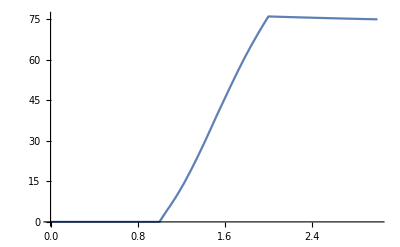

```mathematica
Flatten[Evaluate[outputVar/. solutionList [1] /. t-> 3]]
Plot[Evaluate[outputVar /. solutionList[1], {t,0,3}]]
```

```mathematica
<< HypothesisTesting`

(*Calculate PRCC*)
GammaMatrix={};
InputMatrix={};

sample = 0.005;
For[i=1,i≤nRuns,i++,InputMatrixLine={};
For[j=1,j≤numParams,j++,
InputMatrixLine=AppendTo[InputMatrixLine,paramList[[j,4,i]]]];data = Table[Flatten[Evaluate[outputVar/. solutionList [i] /. t->3]],1];
(*data = Table[datalist[[q]][[1]][[1]][[1]],{q,1,Length[datalist]}];*)
InputMatrixLine=Flatten[AppendTo[InputMatrixLine,data]];
InputMatrix=Append[InputMatrix,InputMatrixLine]];

InputMatrixT=Transpose[InputMatrix];
RankMatrix={};

For[i=1,i≤(numParams+1),i++,ParameterValues=InputMatrixT[[i]];SortedParameterValues=Sort[ParameterValues];For[j=1,j≤nRuns,j++,ParameterValues[[j]]=Position[SortedParameterValues,ParameterValues[[j]]]];ParameterValues=Flatten[ParameterValues];RankMatrix=AppendTo[RankMatrix,ParameterValues]];
mu=(nRuns+1)/2;

cMatrix={};


For[i=1,i≤(numParams+1),i++,cMatrixLine={};For[j=1,j≤(numParams+1),j++,n=0;For[k=1,k≤nRuns,k++,n+=((RankMatrix[[i]][[k]]-mu)*(RankMatrix[[j]][[k]]-mu))];iDenomSum=jDenomSum=0;For[k=1,k≤nRuns,k++,iDenomSum+=((RankMatrix[[i]][[k]]-mu)^2)];For[k=1,k≤nRuns,k++,jDenomSum+=((RankMatrix[[j]][[k]]-mu)^2)];Denom=Sqrt[iDenomSum*jDenomSum];cMatrixLine=Flatten[AppendTo[cMatrixLine,N[n/Denom]]]];cMatrix=AppendTo[cMatrix,cMatrixLine]]; 

bMatrix=Inverse[cMatrix];


For[i=1,i≤numParams,i++,GammaValue=-1*(bMatrix[[i]][[numParams+1]])/(Sqrt[(bMatrix[[i]][[i]])*(bMatrix[[numParams+1]][[numParams+1]])]);GammaMatrix=AppendTo[GammaMatrix,GammaValue]];
GammaMatrix=Partition[Flatten[GammaMatrix],numParams]

(*Export PRCC values to Excel*)
Export["GammaMatrix_Zhabotinsky_10fold_100Hz_n1050_11122018.csv",GammaMatrix];
SystemOpen["GammaMatrix_Zhabotinsky_10fold_100Hz_n1050_11122018.csv"];
```

{{0.0183425,-0.611191,0.783621,0.0123081,0.0326538,0.0827403,-0.296225,0.675902,-0.0229277,-0.00475794,0.693951,-0.30395}}